# MiniData Test and Other Hoardables

Mumble

## Preliminaries

Mumble

Arrow3D

Useful visual object, not supplied with Mathematica system (roll this up)

```mathematica
Options[Arrow3D]={
HeadScaling3D->Relative,
HeadLength3D->0.10,
HeadWidth3D->0.5,
HeadSegments3D->10};
Arrow3D[base:{_,_,_},tip:{_,_,_},___]/;base==tip:=Point[base];
Arrow3D[base:{_,_,_},tip:{_,_,_},opts___?OptionQ]:=
Module[{length,halfwidth,polys,scaletype,scale,anOrthogonalVector,normalize,rotationmatrix,mycone},
anOrthogonalVector[norm:{_,_,_}]:=
	Block[{pos,a,b,v1},
		pos=If[VectorQ[norm,NumberQ],Abs[N[norm]],norm];
		pos=Sort[Transpose[{pos,Range[3]}]];
		{pos,a,b}=Map[Last,pos];
		v1=ReplacePart[{0,0,0},-Part[norm,a],b];
		ReplacePart[v1,Part[norm,b],a]];
normalize[vec_]:=vec/√(vec.vec);
rotationmatrix[axis_,θ_]:=
	Module[{n1,n2,n3},
		{n1,n2,n3}=normalize[axis]//N;
		{{n1^2+(1-n1^2)Cos[θ],n1 n2(1-Cos[θ])+n3 Sin[θ],n1 n3(1-Cos[θ])-n2 Sin[θ]},{n1 n2(1-Cos[θ])-n3 Sin[θ],n2^2+(1-n2^2)Cos[θ],n2 n3(1-Cos[θ])+n1 Sin[θ]},{n1 n3(1-Cos[θ])+n2 Sin[θ],n2 n3(1-Cos[θ])-n1 Sin[θ],n3^2+(1-n3^2)Cos[θ]}}//N
		];
mycone[vec_,tipp_,polys_,halfwidth_,length_]:=
	Block[{norm=normalize[anOrthogonalVector[vec]],θ,Δθ=2π/polys,nvec=normalize[vec]},
		Table[Polygon[{tipp,tipp+halfwidth (norm.rotationmatrix[vec, θ])-length nvec,tipp+halfwidth (norm.rotationmatrix[vec, θ+Δθ])-length nvec}],{θ,0,2π-Δθ,Δθ}]//N];

scaletype=HeadScaling3D/.{opts}/.Options[Arrow3D];
length=HeadLength3D/.{opts}/.Options[Arrow3D];
halfwidth=(HeadWidth3D/.{opts}/.Options[Arrow3D])/2;
polys=HeadSegments3D/.{opts}/.Options[Arrow3D];
polys=Max[2,polys];
scale=If[scaletype===Relative,√((tip-base).(tip-base)),scaletype];
length=length*scale;
halfwidth=length*halfwidth;

{Line[{base,base+0.999(tip-base)}],mycone[tip-base,tip,polys,halfwidth,length]}]
```

```mathematica
Graphics3D[Arrow3D[{0,0,0},{1,1,1}]]
```

-Graphics3D-

Test-Patterns: xcube, wcube; s3p, s3q

```mathematica
o3=ConstantArray[0,3];
```

```mathematica
c3[constant_]:=ConstantArray[constant,3]
```

```mathematica
x3={1,0,0};y3={0,1,0};z3={0,0,1};a3={1,1,1};
```

```mathematica
axesLabel3={"x","y","z"};
```

```mathematica
vcube=
Translate[
{Style[{
Polygon[{o3,x3,a3-z3,y3}],
Polygon[{z3,a3-y3,a3,a3-x3}]},
FaceForm[Blue,Yellow]],
Style[{
Polygon[Reverse[{y3,a3-z3,a3,a3-x3}]],Polygon[Reverse[{o3,x3,a3-y3,z3}]]},
FaceForm[Green,Magenta]],
Style[{
Polygon[{o3,y3,a3-x3,z3}],
Polygon[{x3,a3-z3,a3,a3-y3}]},
FaceForm[Red,Cyan]]
},c3[-.5]];
```

```mathematica
s3p=Show[Graphics3D[{Opacity[0.80],#1},
FaceGrids->All,
Axes->True,
AxesLabel->axesLabel3 (*,Lighting->"Neutral"*),
RotationAction->"Clip"],
ImageSize->Automatic]&;
```

```mathematica
s3q=Show[Graphics3D[{Opacity[0.80],#1},
FaceGrids->All,
Axes->True,
AxesLabel->axesLabel3 ,
Lighting->"Neutral",
RotationAction->"Clip"],
ImageSize->Automatic]&;
```

```mathematica
s3p[vcube]
```

-Graphics3D-

```mathematica
s3q[vcube]
```

-Graphics3D-

```mathematica
vcubePlus=Translate[vcube,a3/2.];
```

```mathematica
x2pols={Style[{
Polygon[Reverse[
{{1,1,0},{2.5,6,0},{3,6,0},{3,4+1/3,0},{2,1,0}}/12.]],Polygon[Reverse[
{{4,1,0},{3,4+1/3,0},{3,6,0},{3.5,6,0},{5,1,0}}/12.]],Polygon[Reverse[
{{3,6,0},{2.5,6,0},{1,11,0},{2,11,0},{3,7+2/3,0}}/12.]],
Polygon[Reverse[
{{3,6,0},{3,7+2/3,0},{4,11,0},{5,11,0},{3.5,6,0}}/12.]]},
FaceForm[Black,White]]};
```

```mathematica
s3p[x2pols]
```

-Graphics3D-

```mathematica
y2pols={Style[{
Polygon[Reverse[
{{2.5,1,0},{2.5,6,0},{3.5,6,0},{3.5,1,0}}/12.]],
Polygon[Reverse[
{{3,6,0},{2.5,6,0},{1,11,0},{2,11,0},{3,7+2/3,0}}/12.]],Polygon[Reverse[
{{3,6,0},{3,7+2/3,0},{4,11,0},{5,11,0},{3.5,6,0}}/12.]]},
FaceForm[Black,White]]};
```

```mathematica
s3p[y2pols]
```

-Graphics3D-

```mathematica
z2pols={Style[{
Polygon[Reverse[
{{1,1,0},{1.3,2,0},{5,2,0},{5,1,0}}/12.]],
Polygon[Reverse[
{{1.3,2,0},{3.7,10,0},{4.7,10,0},{2.3,2,0}}/12.]],Polygon[Reverse[
{{1,11,0},{5,11,0},{4.7,10,0},{1,10,0}}/12.]]},
FaceForm[Black,White]]};
```

```mathematica
s3p[z2pols]
```

-Graphics3D-

```mathematica
Rotate3[shape_,phi_,theta_,psi_]:=
Rotate[Rotate[Rotate[shape,
Pi-phi,z3],
theta,x3],
Pi-psi,z3]
```

```mathematica
combp=Join[#1,{Translate[#2,{0.5,0,0}]}]&;
```

```mathematica
xy2p=combp[x2pols,y2pols];
```

```mathematica
s3p[{x2pols,Translate[y2pols,{0.5,0,0}]}]
```

-Graphics3D-

```mathematica
yz2p=combp[y2pols,z2pols];
```

```mathematica
zx2p=combp[z2pols,x2pols];
```

```mathematica
face2labels=
Translate[
{Translate[Rotate3[zx2p,Pi,Pi/2,0], x3],Translate[Rotate3[zx2p,Pi,Pi/2,0],{1,1,0}],Rotate3[yz2p,0,-Pi/2,-Pi/2],Translate[Rotate3[yz2p,0,-Pi/2,-Pi/2],x3],xy2p,Translate[xy2p,z3]},c3[-.5]];
```

```mathematica
s3p[xy2p]
```

-Graphics3D-

### oriented cuboid

```mathematica
wcube=Chop[Join[{Scale[vcube,c3[0.99],o3]},{face2labels}]];
```

```mathematica
s3p[wcube]
```

-Graphics3D-

```mathematica
s3q[wcube]
```

-Graphics3D-

```mathematica
wcubePlus=Translate[wcube,a3/2.];
```

```mathematica
thing3={Style[{
Style[Line[{o3,x3}],Red],
Style[Line[{o3,y3}],Green],
Style[Line[{o3,z3}],Blue],
Style[Line[{o3,-x3}],Cyan],
Style[Line[{o3,-y3}],Magenta],
Style[Line[{o3,-z3}],Yellow]},
Thickness[0.010]]};
```

Discovered that nested lists may push and pop graphical attributes. This style seems to be a viable alternative to calling Style everywhere.

```mathematica
thing4={Thickness[0.010],{
{Red,Line[{o3,x3}]},
{Green,Line[{o3,y3}]},
{Blue,Line[{o3,z3}]},
{Cyan,Line[{o3,-x3}]},
{Magenta,Line[{o3,-y3}]},
{Yellow,Line[{o3,-z3}]}}
};
```

```mathematica
xcube=Join[{Scale[thing4,c3[2],o3]},{wcube}];
```

```mathematica
s3q[xcube]
```

-Graphics3D-

```mathematica
xcubePlus=Translate[xcube,a3/2.];
```

Transformation Matrices

Predefined in MMA

```mathematica
TfFromMatrix=LinearFractionalTransform;
```

```mathematica
TfIdentity[dim_]:=TfFromMatrix[IdentityMatrix[dim+1]];
```

Mini Data Library

## Definitions

An [association list] is a list of [attributes], that is, [key]-[value] pairs (or, perhaps later, pairs of keys and value-[type] pairs), where the keys are always strings (or symbols? UNDONE) and the values can be anything. E.g., {{"foo", 1}, {"bar", 2}}. No duplicate keys allowed, order is not significant. They're really denumerable sets, but realized as lists for convenience. Use lookup[alist, key] to get the value associated with key from the association list alist.

An [association vector] is a partial function from strings to values (or value-type pairs, or perhaps symbols (UNDONE)). Expressions for looking up values by key have the form of function calls, that is, if v is an association vector and k is a key, write the associated value as v[k]. Association lists and association vectors are in one-to-one correspondence because the domain, strings, is denumerable. Functions are single-valued, meaning that each input string maps to a unique output value, implying that association lists may not have duplicate keys.

There difference between an attribute and a [property], which is also a key-value pair, is that property getters and setters may do significant computation, but attribute setters and getters never do. For instance, a representation for complex numbers may store the real and imaginary parts, and also have properties for getting and setting the modulus and argument, related to the real and imaginary types by coordinate transforms.

Association vectors are the primary vehicle for structured storage. Association lists are convenient for presentation and for some manipulations. Since they are identical in form and function, use the term [association] or [dictionary] to refer generically to these two kinds of data structure.

The implementation automatically stringulates arguments of type <key>.

IndexOfMaxs[<list>, <valueFunction>] --> <integerIndex>
IndexOfMins[<list>, <valueFunction>] --> <integerIndex>
al2Av[<aList>] --> <aVec>
lookup[<aList>,<key>] --> <value>
lookupWithDefault[<aList>,<key>,<default>] --> <value> or <default>
containsKey[<aList>, <key>] --> <bool>
removeKey[<aList>, <key>] --> <aVec>
fetchAttribute[<aList>, <key>] --> {<key>, <value>}
adjoin[<aList>, <key>, <value>] --> <aList>
adjoin[<aList>, <aList>] --> <aList>
getSchema[<aList>] --> {<key>, ...}
schemaAndRecord2Al[<schema>, <record>] --> <aList>
sieve[<aList>, <keyList>] --> {<aList(matchingKeys)>, <aList(notMatchingKeys)>}

// <aVec>[<key>] --> <value>
// lookup[<aVec>,<key>] --> <value>
// lookupWithDefault[<aVec>,<key>,<default>] --> <value> or <default>
// containsKey[<aVec>, <key>] --> <bool>
// removeKey[<aVec>, <key>] --> <aVec>
// fetchAttribute[<aVec>, <key>] --> {<key>, <value>}
// copyAv[<aVec>] --> <aVec>
// equalAvs[<aVec1>, <aVec2>] --> <bool>
// adjoin[<aVec>, <key>, <value>] --> <aVec>
// adjoin[<aVec>, <aList>] --> <aVec>
// adjoin[<aVec>, <aVec>] --> <aVec>
// av2Al[<aVec>] --> {{<key>, <value>}, ...}
// getSchema[<aVec>] --> {<key>, ...}
// schemaAndRecord2Av[<schema>, <record>] --> <aVec>
// sieve[<aVec>, <keyList>] --> {<aVec(matchingKeys)>, <aVec(notMatchingKeys)>}

```mathematica
?isAl
```

Information::notfound: Symbol TraditionalForm`"isAl" not found.

```mathematica
?al2Av
```

Information::notfound: Symbol TraditionalForm`"al2Av" not found.

```mathematica
al2Av[32]
```

al2Av(32)

```mathematica
?equalAvs
```

Information::notfound: Symbol TraditionalForm`"equalAvs" not found.

```mathematica
Needs["MiniData`","Documents\\MMA\\Packages\\MiniData.m"]
```

al2Av::shdw: Symbol TraditionalForm`"al2Av" appears in multiple contexts TraditionalForm`{"MiniData`", "Global`"}; definitions in context TraditionalForm`"MiniData`" may shadow or be shadowed by other definitions.

```mathematica
?lookup
```

lookup[<alist|aVec>,<key>] --> <value>, <avec>[<key>] --> <value>

```mathematica
?lookupWithDefault
```

lookupWithDefault[<alist|aVec>,<key>,<default>] --> <value> or <default>

```mathematica
?containsKey
```

containsKey[<aList|aVec>,<key>] --> <bool>

```mathematica
?removeKey
```

removeKey[<aList|aVec>,<key>] --> <aList> or <aVec>

## Unit Testing the Package

### IndexOfMaxs, IndexOfMins

```mathematica
IndexOfMaxs[{2,3,1}]
```

2

```mathematica
IndexOfMaxs[{2,3,1},#&]
```

2

```mathematica
IndexOfMaxs[{2,3,1},-#&]
```

3

```mathematica
IndexOfMaxs[Range[1000]]
```

1000

```mathematica
IndexOfMins[{2,3,1}]
```

3

```mathematica
IndexOfMins[Range[1000],Sin]
```

344

```mathematica
IndexOfMins[Range[1000],(-#)&]
```

1000

```mathematica
IndexOfMins[RandomSample[Range[1000]]]
```

862

```mathematica
IndexOfMins[{}]
```

0

```mathematica
IndexOfMaxs[{},Sin]
```

0

### (isAl) Is Association List, (isAv) Is Association Vector

### (al2Av) Association List To Association Vector

```mathematica
z = al2Av[{{"name", Unique[]}, {"lon", 100}, {"lat", 100}}];
```

```mathematica
z["name"]
```

$3

```mathematica
isAl[z]
```

isAl(MiniData`Private`d$762)

```mathematica
?equalAvs
```

equalAvs[<aVec>,<aVec>] --> bool

```mathematica
equalAvs[z,al2Av@{{"name", Unique[]}, {"lon", 100}, {"lat", 100}}]
```

False

```mathematica
equalAvs[z,z]
```

True

```mathematica
equalAvs[z,copyAv@z]
```

True

```mathematica
z2=copyAv@z
```

MiniData`Private`d$775

```mathematica
z["name"]=Unique[]
```

$5

```mathematica
equalAvs[z,z2]
```

False

```mathematica
isAv[z]
```

True

```mathematica
z["lon"]
```

100

```mathematica
z
```

MiniData`Private`d$762

```mathematica
Evaluate@z
```

MiniData`Private`d$762

```mathematica
DownValues@z
```

{}

```mathematica
DownValues[Evaluate@z]
```

{HoldPattern[MiniData`Private`d$762(lat)]:>100,HoldPattern[MiniData`Private`d$762(lon)]:>100,HoldPattern[MiniData`Private`d$762(name)]:>$5}

### (av2Al) Association Vector to Assoction List

```mathematica
av2Al[Unique[]]
```

{}

```mathematica
av2Al[{}]
```

{}

```mathematica
??av2Al
```

av2Al[<aVec>] --> <aList>

av2Al[MiniData`Private`d_Symbol]:=With[{MiniData`Private`al=Sort[Union[({#1⟦1,1,1⟧,#1⟦2⟧}&)/@DownValues[MiniData`Private`d]]]},MiniData`Private`av2Alα/@MiniData`Private`al]
 
av2Al[MiniData`Private`x_]:=MiniData`Private`x

```mathematica
av2Al[100]
```

100

```mathematica
av2Al[zzz]
```

{}

```mathematica
av2Al[z]
```

(lat | 100
lon | 100
name | $5)

### (as2Al) Association to AList

### (getSchema) Get Schema

```mathematica
getSchema[{{"name", Zark},{"lon",300},{"lat",300}}]
```

{lat,lon,name}

```mathematica
getSchema[z]
```

{lat,lon,name}

### (schemaAndRecord2Al, schemaAndRecord2Av)

```mathematica
av2Al@schemaAndRecord2Av[{"name", "lat", "lon"}, {Unique[], 120, 130}]
```

(lat | 120
lon | 130
name | $7)

### (copyAv, equalAvs, adjoin)

```mathematica
DownValues@Evaluate@copyAv[z]
```

{HoldPattern[MiniData`Private`d$807(lat)]:>100,HoldPattern[MiniData`Private`d$807(lon)]:>100,HoldPattern[MiniData`Private`d$807(name)]:>$5}

```mathematica
equalAvs[z, copyAv@z]
```

True

A smart adjoin can share the parts of structures that do not change. Structure sharing is not observable with immutables. This dumb adjoin just copies the structure and (invisibly) mutates the copy:

```mathematica
av2Al@adjoin[z, {{"foo", 1}, {"lon", 200}}]
```

(foo | 1
lat | 100
lon | 200
name | $5)

```mathematica
z2 = adjoin[z, "lat", 200];
```

```mathematica
av2Al@z2
```

(lat | 200
lon | 100
name | $5)

```mathematica
av2Al@z
```

(lat | 100
lon | 100
name | $5)

```mathematica
av2Al[adjoin[z, z2]]
```

(lat | 200
lon | 100
name | $5)

```mathematica
av2Al[adjoin[z2, z]]
```

(lat | 100
lon | 100
name | $5)

```mathematica
adjoin[av2Al@z, "lat", 200]
```

(lat | 200
lon | 100
name | $5)

```mathematica
adjoin[av2Al@z, "fon", "fun"]
```

(fon | fun
lat | 100
lon | 100
name | $5)

```mathematica
adjoin[av2Al@z, {{"name", Zark}, {lon, 300}, {"lat", 300}}]
```

(lat | 300
lon | 300
name | Zark)

### (containsKey, removeKey)

```mathematica
containsKey[{{"name", Zark},{"lon",300},{"lat",300}}, lon]
```

True

```mathematica
containsKey[{}, fon]
```

False

```mathematica
containsKey[{{"name", Zark},{"lon",300},{"lat",300}}, fon]
```

False

```mathematica
containsKey[al2Av@{{"name", Zark},{"lon",300},{"lat",300}},fon]
```

False

```mathematica
containsKey[al2Av@{{"name", Zark},{"lon",300},{"lat",300}},lon]
```

True

```mathematica
containsKey[{{"name", Zark},{"lon",300},{"lat",300}}, fon]
```

False

```mathematica
containsKey[z, "long"]
```

False

```mathematica
containsKey[z, "lon"]
```

True

```mathematica
removeKey[{{"name", Zark},{"lon",300},{"lat",300}}, lon]
```

(name | Zark
lat | 300)

```mathematica
av2Al@removeKey[al2Av@{{"name", Zark},{"lon",300},{"lat",300}}, lon]
```

(lat | 300
name | Zark)

```mathematica
removeKey[{{"name", Zark},{"lon",300},{"lat",300}}, fon]
```

(name | Zark
lon | 300
lat | 300)

```mathematica
removeKey[{}, lon]
```

{}

```mathematica
av2Al[removeKey[z, "lon"]]
```

(lat | 100
name | $5)

```mathematica
av2Al[removeKey[z, "long"]]
```

(lat | 100
lon | 100
name | $5)

```mathematica
av2Al[al2Av[{}]]
```

{}

```mathematica
av2Al[removeKey[al2Av[{}], "bar"]]
```

{}

```mathematica
av2Al[removeKey[al2Av[{}], bar]]
```

{}

### (fetchAttribute)

```mathematica
?fetchAttribute
```

fetchAttribute[<aList|aVec>,<key> --> {<key>,<value>}

```mathematica
fetchAttribute[{{"foo",1},{"bar",2}},"foo"]
```

{foo,1}

```mathematica
fetchAttribute[{{"foo",1},{"bar",2}},"fob"]
```

{}

### (lookup, lookupWithDefault)

#### For ALists:

```mathematica
lookup[{{"foo",1},{"bar",2}},"foo"]
```

1

```mathematica
lookup[{{"foo",1},{"bar",2}},"fob"]===Null
```

True

```mathematica
lookupWithDefault[{{"foo",1},{"bar",2}},"foo",42]
```

1

```mathematica
lookupWithDefault[{{"foo",1},{"bar",2}},"fob",42]
```

42

#### for association vectors

```mathematica
fetchAttribute[z, lon]
```

{lon,100}

```mathematica
fetchAttribute[z, "lon"]
```

{lon,100}

```mathematica
fetchAttribute[z, "foo"]
```

```mathematica
fetchAttribute[z, "foo"]===Null
```

True

```mathematica
lookup[z, foo] === Null
```

True

```mathematica
lookupWithDefault[z, "lon", 42]
```

100

```mathematica
lookupWithDefault[z, "foo", 42]
```

42

### (adjoin)

```mathematica
?adjoin
```

adjoin[<aList|aVec>,<key>,<value>] --> <aList|aVec>; adjoin[<aList1|aVec1>,<aList|aVec>] --> <aList|aVec>

```mathematica
av2Al@z
```

(lat | 100
lon | 100
name | $5)

```mathematica
av2Al@adjoin[z,"foo",42]
```

(foo | 42
lat | 100
lon | 100
name | $5)

#### av, al

```mathematica
av2Al@adjoin[z,{{"foo",42}}]
```

(foo | 42
lat | 100
lon | 100
name | $5)

#### al, al

```mathematica
adjoin[av2Al@z,{{"foo",42}}]
```

(foo | 42
lat | 100
lon | 100
name | $5)

#### al, av

```mathematica
adjoin[av2Al@z,al2Av@{{"foo",42}}]
```

(foo | 42
lat | 100
lon | 100
name | $5)

#### av, av

```mathematica
av2Al@adjoin[z,al2Av@{{"foo",42}}]
```

(foo | 42
lat | 100
lon | 100
name | $5)

### (sieve)

```mathematica
?sieve
```

sieve[<aList|aVec>,<keyList>] --> {<aVec(matchingKeys)>,<aVec(notMatchingKeys)>}

```mathematica
sieve[{{"foo",1},{"bar",2},{"baz",3},{"qux",4}},{"boo","far"}]
```

{{},(foo | 1
bar | 2
baz | 3
qux | 4)}

```mathematica
sieve[{{"foo",1},{"bar",2},{"baz",3},{"qux",4}},{"qux","bla","foo"}]
```

({foo,1} | {qux,4}
{bar,2} | {baz,3})

```mathematica
sieve[{{"foo",1},{"bar",2},{"baz",3},{"qux",4}},{}]
```

{{},(foo | 1
bar | 2
baz | 3
qux | 4)}

```mathematica
sieve[{},{"qux","bla","foo"}]
```

{{},{}}

```mathematica
av2Al /@ sieve[al2Av@{{"foo", 1}, {"bar", 2}, {"baz", 3}, {"qux", 4}}, {"qux", "bla", "foo"}]
```

({foo,1} | {qux,4}
{bar,2} | {baz,3})

### getSchema

```mathematica
?getSchema
```

getSchema[<aList|aVec>] --> {<key>, ...}

```mathematica
getSchema@z
```

{lat,lon,name}

### schemaAndRecord2Al

```mathematica
?schemaAndRecord2Al
```

schemaAndRecord2Al[<schema>,<record>] --> <aList>

```mathematica
schemaAndRecord2Al[getSchema@z,{1,2,3}]
```

(lat | 1
lon | 2
name | 3)

```mathematica
?schemaAndRecord2Av
```

schemaAndRecord2Av[<schema>,<record>] --> <aVec>

## Examples

d = al2Av[{{"foo", 1}, {"bar", 2}}] 
will present as the association list {{"foo", 1}, {"bar", 2}}

d["foo"] --> 1

containsKey[d, "foo"] --> True

e = removeKey[d, "foo"]
will present as the association list {{"bar", 2}}

fetchAttribute[d, "foo"] --> {"foo", 1}

f = copyAv[d] (not strictly necessary, but see equalAvs) 
will present as the association list {{"foo", 1}, {"bar", 2}}

equalAvs[d, f] --> True

g = adjoin[d, "baz", 3]
will present as the association list {{"foo", 1}, {"bar", 2}, {"baz", 3}}

Also use adjoin to "change" values, meaning, to write a new association from an old one with the named attribute changed.

av2Al[d] --> {{"foo", 1}, {"bar", 2}}

av2Schema[d] --> {"foo", "bar"}

schemaAndRecord2Av[{"foo", "bar"}, {1, 2}] 
will present as the association list {{"foo", 1}, {"bar", 2}}

### experimental variation including types

UNFINISHED

av2Schema[d] --> {{"foo", Integer}, {"bar", Integer}}

schemaAndRecord2Av[{{"foo", Integer}, {"bar", Integer}}, {{1, {1}}, {2, {2}}}] 
will present as the association list {{"foo", 1, Integer}, {"bar", 2, Integer}}

When combining the record with the schema, check that the data type of each value in the record is a subset of the type described in the schema. If so, take the resulting type from the schema, as it is the "most permissible" or "most permissive."

This should check as equal to {{"foo", 1, {1, 2}}, {"bar", 2, {1, 2}}} and a host of others. Type judgement questions will be questions about membership in sets or about subset relationships. The smallest enclosing set for the value 1 is {1}. 1 is a member of any set that is a superset of {1}, so the quesion "is 1 of type T?" is equivalent to the question "is {1} a subset of T?"

By re-defining a [value] as a pair of a [member] or [element] or [witness] of a [type] qua a set of values (or a name of a set of values, or a reference to a set of values), we perhaps become compatible with the type system recorded in the next subsection:

d = al2Av[{{"foo", 1, Integer}, {"bar", 2, Integer}}]

d["foo"] --> {1, Integer}

containsKey[d, "foo"] --> True

e = removeKey[d, "foo"] --> will present as the association list {{"bar", 2, Integer}}

fetchAttribute[d, "foo"] --> {"foo", 1, Integer}

f = copyAv[d] --> (not strictly necessary, but see equalAvs) will present as the association list {{"foo", 1, Integer}, {"bar", 2, Integer}}

equalAvs[d, f] --> True

g = adjoin[d, "baz", 3] --> will present as the association list 
{{"foo", 1, Integer}, {"bar", 2, Integer}, {"baz", 3, Integer}}

av2Al[d] --> {{"foo", 1, Integer}, {"bar", 2, Integer}}

### Gavin & Erik's Type System

LANGUAGE GEM
gmb & emeijer

Started: 16.10.2008
===================

D ::= N = E             // name declaration
   |  N in E            // type assertion
                        // ?? What about symbolic constants????

E ::= E in E            // check the type                    ???
  |   E : E             // assert the type                   ???
  |   x
  |   \x.E
  |   E(E)
  |   {}
  |   {E}
  |   bind x <- E in E     // comprehensions 
  |   {n1=E1,...,nn=En}    // records
  |   E.n
  |   E?E:E
//
  |   Integer32
  |   Logical 
  |   Text
  |   Entity
  |   Collection
  |   Any
  |   Function  
  
Let's go with a bi-directional system

Inference for entity element selection:

E -> S ~~> E'
DOT(S,n) = YES(T)
-----------------
!E.n -> ?T ~~> ?E'.n

This is an implication diagram, like a set of Prolog Horn clauses. 

The operational reading of this is "construct a proof for the consequent given the implication and potential instantiations for the variables ?T and ?E'"

Read the first clause like this: The act of inferring that expression E has the inferred type S is witnessed by the translation of E into E'
x -> int ~~> (int)x
Type information that's implicit in E is explicit in E'. That's what "witness" means.
x + y -> int ~~> (int)x (int-plus) (int)y
E is the source code, E' is the target code (stylized compilation).

[Reading the bottom] If I have an accessor on an expression, namely E.n, first type-check E, inferring type S and creating witness E'; now call the solver and ask "Does type S have a property n, and, if so, what's its type," and solver answers "YES(T)."

Now we know that accessing n on E has type T, and that the translation of the whole thing is E'.n, this could be read (T)((S)E.n)

(more abstractly, admitting the possibility of properties in addition to field accessors, allow the solver to return the accessor function f :: S -> T)

YES(T,f) where f is the accessor function, and the witness is f(E') ~=~ E'.n

Expression -> (has type) Type ~~> (translates into) Expression'


E -> S ~~> E'
DOT(S,n) = DUNNO
---------------------------------
E.n -> ANY ~~> (E' : {n : ANY}).n
                ^^^^^^^^^^^^^
                runtime test 
                that E has field n

Bug Fix ...

E -> S ~~> E'
DOT(S,n) = DUNNO
runtimeCheck(E') = [E' -> Z ~~> E''
                    DOT(Z,n) = YES(out f)
                    return f(E'')]
-----------------------------------------
E.n -> ANY ~~> runtimeCheck(E')

To infer the type of E.n, first infer the type S of E and construct a witness E' (just as before), now ask the solver whether S has a field n (or accessor function f), and solver says "DUNNO". Now infer that E.n has type ANY and translate E.n into a runtime test (or cast or assertion, the : operator), that E' must have a field (or accessor function) of (or returning) type ANY; and construct the witness E'.n just as before.

At runtime, find the runtime type, Z, of E', call the solver at runtime DOT(Z,n), which should (as always) return YES(out f) NO or DUNNO => both are runtime errors.



                
Now checking for entity selection

E -> S ~~> E'
DOT(S,n) = YES(T)
-----------------
E.n <- T ~~> E'.n

E -> S ~~> E'
DOT(S,n) = DUNNO
-----------------------------
E.n <- T ~~> (E' : {n : T}).n
              ^^^^^^^^^^^^
              runtime test
              that E' has field n
              at type T


Now for entity construction:

Checking:

DOT(T,n) = YES(S)
E <- S ~~> E'
---------------------
{n=E} <- T ~~> {n=E'}

DOT(T,n) = DUNNO
E -> S ~~> E'
--------------------------
{n=E} <- T ~~> ({n=E'} : T)


[So it seems that the ":" is the runtime version of the "<-" relation]


Synthesis:

E -> S ~~> E'
----------------------------
{n=E} -> {n : S} ~~> {n=E'} 


Now for function application:

Checking:

F -> S ~~> F'
A -> T ~~> A
APPLY(S,T) = YES(U)
----------------------------
F(A) <- U ~~> F'(A')

F -> S ~~> F'
A -> T ~~> A'
APPLY(S,T) = DUNNO
-------------------------------
F(A) <- U ~~> (F': T -> U)(A')

Synthesis:

F -> S ~~> F'
A -> T ~~> A'
APPLY(S,T) = YES(U)
----------------------------
F(A) -> U ~~> F'(A')

F -> S ~~> F'
A -> T ~~> A'
APPLY(S,T) = DUNNO
----------------------------------
F(A) -> Any ~~> (F': T -> Any)(A')


Lambda expressions:

Checking:

x:T |- E -> U ~~> E'
exists T. APPLY(S,T) = U
-------------------------
\x.E <- S ~~> \x.E'

x:T |- E -> U ~~> E'
dunno exists T. APPLY(S,T) = U
-------------------------------
\x.E <- S ~~> (\x.E' : S)

Synthesis:

x:Any |- E -> S ~~> E'
------------------------
\x.E -> (Any -> S) ~~> \x.E'

Mini Object Library

Anything that's an "object" in our world must have an attribute named "$type." The following test and fetch the values of that attribute. FOR NOW, values of this attribute are just uninterpreted names.

```mathematica
GetType[obj_]:=lookup[obj,"$type"];
```

```mathematica
Is[obj_,type_]:=GetType[obj]===type;
```

Later, after dtmm, define changeType[newType_]:=dtmm[newType&][{"$type"}]

## Inheritance

UNFINISHED: For now, there is no implementation of inheritance or of the "is-a" and "has-a" relations. Instead, just represent such facts explicitly, by copy-paste.

Data Transformers

A [data transformer (Dt)] takes an association list (or association vector) and transforms certain members contained in it, returning a new association list (or association vector) containing both the unchanged attributes and the changed attributes.

A [data transformer maker (Dtm)] takes a schema and returns a data transformer that will transform members whose keys match those given in the schema.

A [data transformer maker maker (Dtmm)] takes a pair of transformation functions, one for transforming the key of an attribute and one for transforming the value of an attribute, and returns a data transformer maker.

```mathematica
Pair[x_,y_]:={x,y};
```

```mathematica
Second[thing_]:=thing⟦2⟧;
```

```mathematica
Remove[idDtm,logDtm,capDtm,dtmm,selectDtmm,dtJoin,dropDtm,keepDtm,dtUnit]
```

## The id Dtm

The id Dtm takes a schema and returns a Dt (function of an association list) that does not change the association. The id Dtm ignores its input schema.

```mathematica
idDtm[schema_List]:=#&;
```

```mathematica
testData=RandomSample@
{{"Result",R},
{"NVotes",3000},
{"Precinct",alameda},
{"foo",5},
{"bar",6},
{"baz",7},
{"qux",8},
{"blargh",9}}
```

(bar | 6
qux | 8
baz | 7
Precinct | alameda
NVotes | 3000
blargh | 9
foo | 5
Result | R)

```mathematica
idDtm[{"Result"}]@testData
```

(bar | 6
qux | 8
baz | 7
Precinct | alameda
NVotes | 3000
blargh | 9
foo | 5
Result | R)

```mathematica
idDtm[{"foo","bar"}]@testData
```

(bar | 6
qux | 8
baz | 7
Precinct | alameda
NVotes | 3000
blargh | 9
foo | 5
Result | R)

## The Log Dtm

The log Dtm takes a schema and returns a Dt function that will take the log of any attributes whose keys match those in the given schema. The Dt returned by the log Dtm transforms both the key of the matching attribute and the value of the matching attribute. It changes the key by wrapping it in a "Log10(...)" notation, and it changes the value by actually taking the log base 10.

```mathematica
logDtm[schema_List]:=
Function[aList,
Map[
Function[attribute,
Module[{atkey,atval},
{atkey,atval}=attribute;
If[MemberQ[schema,atkey],
Pair[
StringJoin["Log10(",atkey,")"],
Log[10,N[atval]]],
attribute]]],
aList]];
```

```mathematica
logDtm[{"NVotes"}]@testData
```

(bar | 6
qux | 8
baz | 7
Precinct | alameda
Log10(NVotes) | 3.47712
blargh | 9
foo | 5
Result | R)

## The Dt Composer, dtJoin

Composition of data transformers is straightforward.

```mathematica
dtJoin=Composition;
```

```mathematica
idDtm[{"Ringo"}]@testData
```

(bar | 6
qux | 8
baz | 7
Precinct | alameda
NVotes | 3000
blargh | 9
foo | 5
Result | R)

```mathematica
dtJoin[
idDtm[{"Result"}],
idDtm[{"Ringo"}]]@testData
```

(bar | 6
qux | 8
baz | 7
Precinct | alameda
NVotes | 3000
blargh | 9
foo | 5
Result | R)

```mathematica
dtJoin[
idDtm[{"Result"}],
logDtm[{"NVotes"}]]@testData
```

(bar | 6
qux | 8
baz | 7
Precinct | alameda
Log10(NVotes) | 3.47712
blargh | 9
foo | 5
Result | R)

```mathematica
dtJoin[
idDtm[{"NVotes","foo"}],
logDtm[{"NVotes","bar"}]]@testData
```

(Log10(bar) | 0.778151
qux | 8
baz | 7
Precinct | alameda
Log10(NVotes) | 3.47712
blargh | 9
foo | 5
Result | R)

## The Capitalization Dtm

The Capitalization Dtm takes a schema and returns a Dt that capitalizes the value of any attribute whose key matches any of the keys given in the schema.

```mathematica
capitalize[s_String]:=
StringJoin@
(FromCharacterCode/@
(If[#≥97&&#≤122,#-32,#]&/@
(ToCharacterCode[s])))
```

```mathematica
capDtm[schema_List]:=
Function[aList,
Map[
Function[attribute,
Module[{atkey,atval},
{atkey,atval}=attribute;
If[MemberQ[schema,atkey],
Pair[
atkey,
capitalize[ToString[atval]]],
attribute]]],
aList]];
```

```mathematica
capDtm[{"Precinct","Result","foo"}]@
testData
```

(bar | 6
qux | 8
baz | 7
Precinct | ALAMEDA
NVotes | 3000
blargh | 9
foo | 5
Result | R)

```mathematica
dtJoin[
capDtm[{"Precinct","Result","foo"}],
logDtm[{"NVotes"}]]@
testData
```

(bar | 6
qux | 8
baz | 7
Precinct | ALAMEDA
Log10(NVotes) | 3.47712
blargh | 9
foo | 5
Result | R)

## The Drop Dtm

The Drop Dtm takes a schema and returns a Dt that drops any attributes whose keys match any of the keys in the schema

```mathematica
dropDtm[schema_List]:=
Function[aList,
Select[aList,
Function[attribute,
Module[{atkey,atval},
{atkey,atval}=attribute;
Not@MemberQ[schema,atkey]]]]];
```

```mathematica
dropDtm[RandomSample@{"foo","bar","baz","qux","barbie","ken"}]@
testData
```

(Precinct | alameda
NVotes | 3000
blargh | 9
Result | R)

## The Keep Dtm

The logical converse of the Drop Dtm: this creates a Dt that keeps any attributes with keys matching anything in the schema

```mathematica
keepDtm[schema_List]:=
Function[aList,
Select[aList,
Function[attribute,
Module[{atkey,atval},
{atkey,atval}=attribute;
MemberQ[schema,atkey]]]]];
```

## Data Transformer Maker Makers (Dtmms)

Many Dtms differ only in the transformation function that gets mapped or filtered over. Write Dtmms that build these Dtms

This Dtmm takes a pair of transformation functions, one for keys and one for values, both defaulting to the identity function, and returns a Dtm that will take a schema and return a Dt that applies these functions to attributes in a given association that match any of the keys in the schema:

### Make DTs Work on Association Vectors, too

while we're at it...

```mathematica
id=Function[x,x];
```

```mathematica
Remove[dtmm];
dtmm[valueTransform_:id,keyTransform_:id]:=
Function[schema,(* Dtm returned by this Dtmm *)
Function[assoc,(* Dt returned by the Dtm *)
Map[
Function[attribute,
Module[{atkey,atval},
{atkey,atval}=attribute;
If[MemberQ[schema,atkey],
Pair[
keyTransform[atkey],
valueTransform[atval]],
attribute]]],
assoc]]];
```

```mathematica
Remove[idDtm,logDtm,capDtm];
idDtm=dtmm[];
logDtm=dtmm[Log[10,N@#]&,StringJoin["Log10(",#,")"]&];
capDtm=dtmm[Composition[capitalize,ToString]];
```

```mathematica
capDtm[{"Precinct"}]@testData
```

(bar | 6
qux | 8
baz | 7
Precinct | ALAMEDA
NVotes | 3000
blargh | 9
foo | 5
Result | R)

```mathematica
capDtm[{"Precinct"}]@testData
```

(bar | 6
qux | 8
baz | 7
Precinct | ALAMEDA
NVotes | 3000
blargh | 9
foo | 5
Result | R)

```mathematica
dtJoin[
idDtm[{"Result"}],
logDtm[{"NVotes"}],
capDtm[{"Precinct"}]]@testData
```

(bar | 6
qux | 8
baz | 7
Precinct | ALAMEDA
Log10(NVotes) | 3.47712
blargh | 9
foo | 5
Result | R)

```mathematica
dtJoin[
idDtm[{"Result"}],
logDtm[{"NVotes"}],
capDtm[{"Precinct"}]]@testData
```

(bar | 6
qux | 8
baz | 7
Precinct | ALAMEDA
Log10(NVotes) | 3.47712
blargh | 9
foo | 5
Result | R)

Another kind of Dtmm is one that abstracts over the dropDtm and the keepDtm: a Dtmm takes criterion function of a schema, key, and value and returns a Dtm that will take a schema and return a Dt that will apply the criterion to every member that realizes it. The default for the criterion function is one that always returns true.

```mathematica
Remove[selectDtmm];
selectDtmm[criterion_:Function[{s,k,v},True]]:=
Function[schema,
Function[assoc,(* Dt returned by the Dtm *)
Select[assoc,
Function[attribute,
Module[{atkey,atval},
{atkey,atval}=attribute;
criterion[schema,atkey,atval]]]]]];
```

```mathematica
Remove[dropDtm,keepDtm]
dropDtm=selectDtmm[Function[{s,k,v},Not@MemberQ[s,k]]];
keepDtm=selectDtmm[Function[{s,k,v},MemberQ[s,k]]];
```

```mathematica
dropDtm[RandomSample@{"foo","bar","baz","qux","barbie","ken"}]@testData
```

(Precinct | alameda
NVotes | 3000
blargh | 9
Result | R)

```mathematica
dropDtm[RandomSample@{"foo","bar","baz","qux","barbie","ken"}]@testData
```

(Precinct | alameda
NVotes | 3000
blargh | 9
Result | R)

```mathematica
keepDtm[RandomSample@{"Precinct","NVotes","Result","barbie","ken"}]@testData
```

(Precinct | alameda
NVotes | 3000
Result | R)

```mathematica
keepDtm[RandomSample@{"Precinct","NVotes","Result","barbie","ken"}]@testData
```

(Precinct | alameda
NVotes | 3000
Result | R)

```mathematica
dropDtm[{}]@testData
```

(bar | 6
qux | 8
baz | 7
Precinct | alameda
NVotes | 3000
blargh | 9
foo | 5
Result | R)

```mathematica
dropDtm[{}]@testData
```

(bar | 6
qux | 8
baz | 7
Precinct | alameda
NVotes | 3000
blargh | 9
foo | 5
Result | R)

```mathematica
keepDtm[{}]@testData
```

{}

```mathematica
keepDtm[{}]@testData
```

{}

### Associativity?

```mathematica
dtJoin[
idDtm[{"Result"}],
dtJoin[
logDtm[{"NVotes"}],
capDtm[{"Precinct"}]]]@testData
```

(bar | 6
qux | 8
baz | 7
Precinct | ALAMEDA
Log10(NVotes) | 3.47712
blargh | 9
foo | 5
Result | R)

```mathematica
dtJoin[
idDtm[{"Result"}],
dtJoin[
logDtm[{"NVotes"}],
capDtm[{"Precinct"}]]]@testData
```

(bar | 6
qux | 8
baz | 7
Precinct | ALAMEDA
Log10(NVotes) | 3.47712
blargh | 9
foo | 5
Result | R)

```mathematica
dtJoin[
dtJoin[
idDtm[{"Result"}],
logDtm[{"NVotes"}]],
capDtm[{"Precinct"}]]@testData
```

(bar | 6
qux | 8
baz | 7
Precinct | ALAMEDA
Log10(NVotes) | 3.47712
blargh | 9
foo | 5
Result | R)

```mathematica
dtJoin[
dtJoin[
idDtm[{"Result"}],
logDtm[{"NVotes"}]],
capDtm[{"Precinct"}]]@testData
```

(bar | 6
qux | 8
baz | 7
Precinct | ALAMEDA
Log10(NVotes) | 3.47712
blargh | 9
foo | 5
Result | R)

### Unit?, Left and Right?

```mathematica
dtUnit=idDtm[{}];
```

```mathematica
dtJoin[capDtm[{"Precinct"}],dtUnit]@testData
```

(bar | 6
qux | 8
baz | 7
Precinct | ALAMEDA
NVotes | 3000
blargh | 9
foo | 5
Result | R)

```mathematica
dtJoin[dtUnit,capDtm[{"Precinct"}]]@testData
```

(bar | 6
qux | 8
baz | 7
Precinct | ALAMEDA
NVotes | 3000
blargh | 9
foo | 5
Result | R)

## Older VCE Ideas

Defined first so we can use them below.

[Object] = an association, that is, set of properties, potentially with [behaviors], that is, properties whose values are functions

[Visualizable] = [Vz] = Top of the VCE object hierarchy

[Rectangular prism] = [Rp] = Cuboid

[Shard] = [Canonical Shape] = Atomic visualizable

A [property-setter] [ps] takes an object and returns a new copy infused appropriately with certain attributes (or properties).

Basic Visualizables

Mumble

## Labels

```mathematica
newLabel[content_:"Hello"]:=
{{"content",content},
{"text",Style[content,Blue,Italic,24]},
{"children",{}},
{"localTf",TfIdentity[3]},
{"$type","label"}};
```

```mathematica
newLabel[]
```

(content | Hello
text | Hello
children | {}
localTf | TransformationFunction[(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)]
$type | label)

```mathematica
styleDtm[color_,face_,size_]:=
Function[datum,
adjoin[datum,"text",
Style[lookup[datum,"content"],color,face,size]]];
```

```mathematica
styleDtm[Red,Bold,36]@newLabel[]
```

(children | {}
content | Hello
localTf | TransformationFunction[(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)]
text | Hello
$type | label)

## Rectangular Prism

A geometric primitive with no renderable attributes:

```mathematica
Remove[newBar,newRp]
```

```mathematica
newRp[h_:1,w_:1,d_:1]:=
{{"bounds",{{"height", h}, {"width", w}, {"depth", d}}},
{"localTf",ScalingTransform[{w,d,h}]},
{"children",{}},
{"$type","rectangularPrism"}};
```

Property Setters

## Bounds 2 Rp 2 Rp

bounds2Rp2Rp takes a bounds spec and makes a property setter that applies that bounds spec to a Rp (rectangular prism, a.k.a. cuboid). This sets the local transformation function

```mathematica
Remove[
bounds2Rp2Rp,
color2Vz2Vz,
axisLabels2Bc2Bc,
rp2BoundsVals,
boundsAndRp2Vals]
```

```mathematica
newRp[]
```

(bounds | (height | 1
width | 1
depth | 1)
localTf | TransformationFunction[(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)]
children | {}
$type | rectangularPrism)

```mathematica
rp2BoundsVals[rp_,keys_:{"width","depth","height"}]:=
lookup[lookup[rp,"bounds"],#]&/@keys;
rp2BoundsVals@newRp[]
```

{1,1,1}

Replace the bounds in the rp with the given subset of bounds.

```mathematica
boundsAndRp2Vals[bounds_,rp_,keys_:{"width","depth","height"}]:=
lookupWithDefault[
bounds, 
#,
lookup[lookup[rp,"bounds"],#]]&/@keys;
```

Keep the bounds and the localTf consistent (not sure whether to compose or to overwrite, in general, but overwriting is safer)

```mathematica
bounds2Rp2Rp[bounds_]:=
Module[{keys={"width","depth","height"}},
Function[rp,
Module[{newVals=boundsAndRp2Vals[bounds,rp,keys]},
adjoin[rp,
{{"bounds", MapThread[List,{keys,newVals}]},
{"localTf",ScalingTransform[newVals]}}]]]];
```

The following applies a data binding to a particular Rp, this time, a bar:

```mathematica
bounds2Rp2Rp[{{"depth",17}}]@newRp[1,2,3]
```

(bounds | (width | 2
depth | 17
height | 1)
children | {}
localTf | TransformationFunction[(2 | 0 | 0 | 0
0 | 17 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)]
$type | rectangularPrism)

```mathematica
bounds2Rp2Rp[{{"depth",17},{"height",29}}]@newRp[1,2,3]
```

(bounds | (width | 2
depth | 17
height | 29)
children | {}
localTf | TransformationFunction[(2 | 0 | 0 | 0
0 | 17 | 0 | 0
0 | 0 | 29 | 0
0 | 0 | 0 | 1)]
$type | rectangularPrism)

bounds2Rp2Rp just ignores non-geometric attributes, meaning that the property setter it creates will not infuse any non-geometric attributes.

```mathematica
bounds2Rp2Rp[{{"depth",17},{"color",Blue},{"height",29}}]@newRp[1,2,3]
```

(bounds | (width | 2
depth | 17
height | 29)
children | {}
localTf | TransformationFunction[(2 | 0 | 0 | 0
0 | 17 | 0 | 0
0 | 0 | 29 | 0
0 | 0 | 0 | 1)]
$type | rectangularPrism)

## Ps Maker Maker

Here is a psmm that just tacks on new attributes, without doing any new "mini-solves":

```mathematica
Remove[simplePsmm];
simplePsmm[pnyms_List]:=
Function[alist,
Function[vz,
adjoin[vz,keepDtm[pnyms][alist]]]];
```

## Color 2 Vz 2 Vz

A psm that takes a color attribute and makes a property setter that will apply that color to the given visualizable.

```mathematica
color2Vz2Vz=simplePsmm[{"color"}];
```

## AxisLabels 2 Bc 2 Bc

A Bar Chart (Bc) has axis labels. Here's a property setter for such things:

```mathematica
axisLabels2Bc2Bc=simplePsmm[{"axisLabels"}];
```

```mathematica
axisLabels2Bc2Bc[
{{"depth",17},
{"color",Blue},
{"axisLabels",{"Result","Votes","Precinct"}}}]@
newRp[1,2,3]
```

(axisLabels | {Result,Votes,Precinct}
bounds | (height | 1
width | 2
depth | 3)
children | {}
localTf | TransformationFunction[(2 | 0 | 0 | 0
0 | 3 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)]
$type | rectangularPrism)

## Property-Setter Join

```mathematica
Remove[psJoin]
psJoin=Composition;
```

Stitch together the bounds ps and the color ps to get a ps that can do both:

```mathematica
color2Vz2Vz[{{"color",Blue}}]@
bounds2Rp2Rp[{{"depth", 17},{"height",29}}]@
newRp[1,2,3]
```

(bounds | (width | 2
depth | 17
height | 29)
children | {}
color | RGBColor[0,0,1]
localTf | TransformationFunction[(2 | 0 | 0 | 0
0 | 17 | 0 | 0
0 | 0 | 29 | 0
0 | 0 | 0 | 1)]
$type | rectangularPrism)

```mathematica
inspectMe = 
psJoin[
bounds2Rp2Rp[{{"height",29},{"depth", 17}}],
color2Vz2Vz[{{"color", Blue}}]]@
newRp[1, 2, 3]
```

(bounds | (width | 2
depth | 17
height | 29)
children | {}
color | RGBColor[0,0,1]
localTf | TransformationFunction[(2 | 0 | 0 | 0
0 | 17 | 0 | 0
0 | 0 | 29 | 0
0 | 0 | 0 | 1)]
$type | rectangularPrism)

### Associativity?

```mathematica
inspectMe3=
psJoin[
bounds2Rp2Rp[{{"height",29},{"depth",17}}],
color2Vz2Vz[{{"color",Blue}}],
axisLabels2Bc2Bc[{{"axisLabels",{"Result","Votes","Precinct"}}}]]@
newRp[1,2,3]
```

(axisLabels | {Result,Votes,Precinct}
bounds | (width | 2
depth | 17
height | 29)
children | {}
color | RGBColor[0,0,1]
localTf | TransformationFunction[(2 | 0 | 0 | 0
0 | 17 | 0 | 0
0 | 0 | 29 | 0
0 | 0 | 0 | 1)]
$type | rectangularPrism)

### Left and Right Unit?

```mathematica
unit2BarPs=simplePsmm[{}];
psJoin[
bounds2Rp2Rp[{{"depth",17}}],
unit2BarPs[{}]]@
newRp[1,2,3]===
psJoin[
unit2BarPs[{}],
bounds2Rp2Rp[{{"depth",17}}]]@
newRp[1,2,3]
```

True

## Another Combinator for Property Setter Makers

Given a stream of attributes, we may wish to make a composition of property setters made from those attributes. For instance, given the stream, {{"depth", 17}, {"color", Blue}, {"axisLabels", {"Result", "Votes", "Precinct"}}}, we might want to make a Vz2Vz will set all three attributes as described.

How about a function of two associations, one Psms and one of attributes to feed them, then return a composition of the resulting Ps'es?

```mathematica
compositionBuilder[psms_List,attrs_List]:=
Apply[psJoin,Map[#[attrs]&,psms]]
```

```mathematica
testAttrs={
{"depth",17},
{"color",Blue},
{"height",29},
{"axisLabels",{"Result","Votes","Precinct"}}};
```

```mathematica
compositionBuilder[
{bounds2Rp2Rp,color2Vz2Vz,axisLabels2Bc2Bc},
testAttrs]@
newRp[]
```

(axisLabels | {Result,Votes,Precinct}
bounds | (width | 1
depth | 17
height | 29)
children | {}
color | RGBColor[0,0,1]
localTf | TransformationFunction[(1 | 0 | 0 | 0
0 | 17 | 0 | 0
0 | 0 | 29 | 0
0 | 0 | 0 | 1)]
$type | rectangularPrism)

Minard Data

Original Minard data representing the strength of the army at a number of locations on a 2D map. The schema is

```mathematica
{"positionX","positionY","numberOfTroops","unknown"};
```

I do not know what the last number in each list (the 1s and 0s) means. This list is structured one deep; flatten out one level before using. Also, there are records with duplicate positions, always in adjacent slots. Sieve out all but the last of such replicates because we really don't want visualizables plunked down on top of one another with different data.

```mathematica
StrengthData = {
{{0.142, 0.238, 50000, 1},
  {0.257, 0.331, 50000, 1},
  {0.312, 0.326, 50000, 1},
  {0.312, 0.326, 33000, 1},
  {0.392, 0.318, 33000, 0}},
{{0.392, 0.318, 30000, 0},
  {0.433, 0.177, 30000, 0}},
{{0.105, 0.242, 22000, 1},
  {0.111, 0.351, 22000, 1}},
{{0.103, 0.353,  6000, 0},
  {0.0916,0.193,  6000, 0}},
{{0.0565, 0.23, 422000, 1},
  {0.105, 0.242, 422000, 1},
  {0.105, 0.242, 400000, 1},
  {0.181, 0.234, 400000, 1},
  {0.181, 0.234, 340000, 1},
  {0.333, 0.273, 257000, 1},
  {0.476, 0.288, 175000, 1},
  {0.595, 0.250, 145000, 1},
  {0.704, 0.290, 136000, 1},
  {0.789, 0.368, 127000, 1},
  {0.84 , 0.355, 127000, 1},
  {0.84,  0.355, 100000, 1},
  {0.856, 0.349, 100000, 1},
  {0.955, 0.4  , 100000, 1}},
{{0.965, 0.382, 100000, 0},
  {0.953, 0.374, 100000, 0},
  {0.945, 0.312, 100000, 0},
  {0.932, 0.302,  98000, 0},
  {0.838, 0.326,  87000, 0},
  {0.768, 0.296,  87000, 0},
  {0.768, 0.296,  55000, 0},
  {0.7,   0.259,  55000, 0},
  {0.7  , 0.259,  37000, 0},
  {0.612, 0.228,  37000, 0},
  {0.612, 0.228,  24000, 0},
  {0.511, 0.209,  24000, 0},
  {0.511, 0.209,  20000, 0},
  {0.433, 0.177,  20000, 0},
  {0.433, 0.177,  50000, 0},
  {0.390, 0.162,  50000, 0},
  {0.380, 0.164,  50000, 0},
  {0.380, 0.164,  28000, 0},
  {0.316, 0.201,  22000, 0},
  {0.279, 0.181,  22000, 0},
  {0.248, 0.191,  14000, 0},
  {0.158, 0.195,   8000, 0},
  {0.125, 0.193,   8000, 0},
  {0.125, 0.193,   4000, 0},
  {0.0916,0.193,   4000, 0},
  {0.0916,0.193,  10000, 0},
  {0.0682,0.193,  10000, 0}}};
```

```mathematica
Length[Flatten[StrengthData,1]]
```

52

```mathematica
Manipulate[
Take[Module[{raw=Drop[#,-1]&/@Flatten[StrengthData,1]},
{100#⟦1⟧,100#⟦2⟧,Log[N[#⟦3⟧]]}&/@raw],n],
{n,1,52,1}]
```

```mathematica
Manipulate[
Module[{raw=Drop[#,-1]&/@Flatten[StrengthData,1]},
ListPlot3D[
Take[{100#⟦1⟧,100#⟦2⟧,Log[#⟦3⟧]}&/@raw,n],
InterpolationOrder->0,
ColorFunction->"BrightBands",
Mesh->None]],
{n,4,52,1}]
```

UNDONE: Scaling factors must percolate through : inside, need a primitive to replace a list of values with values mapped to [0..1]

Build nested alist. Multiply latitudes and longitudes by 100 to bring them into decent range.

```mathematica
army=
{{"location",{
{"name",Unique[]},
{"lon",100#⟦1⟧},
{"lat",100#⟦2⟧}}},
{"size",#⟦3⟧}}&/@
Flatten[StrengthData,1];
```

```mathematica
Length[army]
```

52

Test accessors:

```mathematica
army⟦29⟧["location"]["lat"]
```

((location | (name | $36
lon | 93.2
lat | 30.2)
size | 98000)(location))(lat)

Bar and Bar-Chart DataTypes

A Bar is a rectangular prism with (potentially) some other attributes. Just copy-and-paste instead of trying to simulate inheritance.

## Bar Constructor

```mathematica
newBar[h_:1,w_:1,d_:1]:=
{{"bounds",{{"height", h}, {"width", w}, {"depth", d}}},
{"localTf",ScalingTransform[{w,d,h}]},
{"children",{}},
{"$type","bar"}};
```

Pick the "size" attribute of every element of army and maps it to the height attribute of a bar, resulting in a list of bars, one for each "size" in army:

### Minard Test Data as Bars

```mathematica
zipApply[listOfUnaryFuncs_List,listOfArgs_List]:=
MapThread[Apply,
{listOfUnaryFuncs,
List/@listOfArgs }](* Apply requires arg LISTS, so one extra level of curlies *)
```

```mathematica
nameChangeDtm[oldNym_,newNym_]:=dtmm[id,newNym&][{oldNym}]
```

```mathematica
(bounds2Rp2Rp@nameChangeDtm["size","height"]@army⟦1⟧)@newBar[]
```

(bounds | (width | 1
depth | 1
height | 50000)
children | {}
localTf | TransformationFunction[(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 50000 | 0
0 | 0 | 0 | 1)]
$type | bar)

```mathematica
unitBars=ConstantArray[newBar[],Length@army];
```

```mathematica
armyBars=zipApply[
bounds2Rp2Rp/@
nameChangeDtm["size","height"]/@
army,
unitBars];
```

```mathematica
fewBars=Take[armyBars,{16, 22}];
```

Convert the name of the "size" attribute to a given bounds attribute and replace its value with log(1+#):

```mathematica
logP1Dtm[boundsNym_String]:=dtmm[Log[N[#+1]]&,boundsNym&][{"size"}]
```

```mathematica
logP1Dtm["height"]@army⟦16⟧
```

(location | (name | $23
lon | 18.1
lat | 23.4)
height | 12.7367)

```mathematica
logBars=
zipApply[
bounds2Rp2Rp/@
logP1Dtm["height"]/@
army,
unitBars];
```

```mathematica
logBars⟦1⟧
```

(bounds | (width | 1
depth | 1
height | 10.8198)
children | {}
localTf | TransformationFunction[(1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 10.8198 | 0.
0. | 0. | 0. | 1.)]
$type | bar)

## New Bar Chart

```mathematica
newBarChart[bars_:{}]:=
{{"axisLabels",Null},
{"children",bars},
{"localTf",TfIdentity[3]},
{"$type","barChart"}};
```

Next, put a list of bars on a "natural" axis made by distributing the bars evenly in the x axis along a line going from 0 to 1 in increments of 1/n, leaving a little space between the bars.

Implicitly encode heights in the z direction of the embedded scaling transform in each bar.

helpers; define them at global scope because they might be generally useful:

Produce n+1 values from 0 through 1 every (1/n)-th of a step:

```mathematica
evenNths[nbars_]:=Table[(i-1)/nbars,{i,1,nbars+1}];
evenNths[3]
```

{0,1/3,2/3,1}

```mathematica
midPoints[nbars_Integer]:=
MapThread[Mean[{#1,#2}]&,
{Drop[evenNths[nbars],-1],
Drop[evenNths[nbars],1]}];
```

```mathematica
midPoints[3]
```

{1/6,1/2,5/6}

Sample-to-sample distances.

```mathematica
deltas[samps_]:=Drop[samps,1]-Drop[samps,-1];
deltas[evenNths[3]]
```

{1/3,1/3,1/3}

Experiment with compositions of transformations to make sure we get the order right:

```mathematica
Manipulate[
Module[{rgx=2,rgy=2,rgz=2},
Graphics3D[{Opacity[0.80],
GeometricTransformation[
xcube,(* Cuboid[o3,a3], *)
Composition[
TranslationTransform[Append[t,0]],
ShearingTransform[s⟦1⟧,{0,0,1},Append[r,0]],
RotationTransform[{x3,Append[r,0]}],
ScalingTransform[{.5,1,1}],
If[f==0,TfIdentity[3],ReflectionTransform[Switch[f,1,x3,2,y3,3,z3]]]]]},
FaceGrids->All,
Axes->True,
AxesLabel->axesLabel3,
RotationAction->"Clip",
PlotRange->{{-rgx,rgx},{-rgy,rgy},{-rgz,rgz}}]],
{t,{-1,-1},{1,1}},
{{f,0,"flip"},0,3,1},
{s,{0,0},{1,1}},
{r,{0.0001,0.0001},{1,1}}]
```

### Transform Composers and Rewriters

Unit values for each of the transformation types, ignoring FLIP (reflection) for now:

```mathematica
unitScoot={0,0,0};
unitSqueeze={1,1,1};
unitTwist={{1,0,0},{1,0,0}};
```

Three arguments in a list -- use Apply (vagaries of the Mathematica interface)

```mathematica
unitShear={0,{1,0,0},{0,0,1}};
```

Ignore flips for now:

```mathematica
unitFlip={};
```

Generic transform-composers and rewriters that operate on any visualizable:

The first form, "transformComposer," is convenient because it's easiest to create the Geometric Transformations as parallel lists rather than as zipped-up packages (requiring an expensive 5-zip). MapThread is natural for applying functions to parallel lists, and that's the pattern we adopt for convenience. However, we also show the property-setter forms of these composers and rewriters.

```mathematica
Remove[transformComposer,transformCompositionPsm,transformRewriter, transformRewritePsm];

transformComposer[vz_,
scoot_:unitScoot,
squeeze_:unitSqueeze,
twist_:unitTwist,
shear_:unitShear,
flip_:unitFlip]:=
(* To the transformation function of the visualizable, adjoin the result of ... *)
adjoin[vz,"localTf",
(* ... composing, with new data in an appropriate order, ... *)
Composition[
(* ... the given scoot vector, ... *)
TranslationTransform[scoot],
(* ... the given shear arguments, ... *)
Apply[ShearingTransform, shear],
(* ... the given rotation expressed as a pair of vectors, ... *)
(* (RotationTransform is not forgiving of the degenerate case, which SHOULD result in the identity transform; take care of that right here *)
If[twist⟦1⟧===twist⟦2⟧, 
TfIdentity[3],
RotationTransform[twist]],
(* ... and the given squeezes in each of three directions, ... *)
ScalingTransform[squeeze],
(* ... with the old transform *)
(* ignore flips for now *)
lookup[vz,"localTf"]]];

transformCompositionPsm[
scoot_:unitScoot,
squeeze_:unitSqueeze,
twist_:unitTwist,
shear_:unitShear,
flip_:unitFlip]:=
Function[vz,
adjoin[vz,"localTf",
Composition[
TranslationTransform[scoot],
Apply[ShearingTransform, shear],
If[twist⟦1⟧===twist⟦2⟧, 
TfIdentity[3],
RotationTransform[twist]],
ScalingTransform[squeeze],
lookup[vz,"localTf"]]]];

transformRewriter[vz_,
scoot_:unitScoot,
squeeze_:unitSqueeze,
twist_:unitTwist,
shear_:unitShear,
flip_:unitFlip]:=
adjoin[vz,"localTf",
Composition[
TranslationTransform[scoot],
Apply[ShearingTransform, shear],
If[twist⟦1⟧===twist⟦2⟧, 
TfIdentity[3],
RotationTransform[twist]],
ScalingTransform[squeeze]]];

transformRewritePsm[
scoot_:unitScoot,
squeeze_:unitSqueeze,
twist_:unitTwist,
shear_:unitShear,
flip_:unitFlip]:=
Function[vz,
adjoin[vz,"localTf",
Composition[
TranslationTransform[scoot],
Apply[ShearingTransform, shear],
If[twist⟦1⟧===twist⟦2⟧, 
TfIdentity[3],
RotationTransform[twist]],
ScalingTransform[squeeze]]]];
```

## Monadic form (UNDONE)

One input, two outputs, streaming "history" through so we can undo property setters. A member of the state-like monad is a function from a state (a quint of scoot, squeeze, twist, shear, and flip) to a pair of state and visualizable. The right-hand side of a Kleisli composition is a function from visualizable to (state, vz) pair.

```mathematica
returnVz[vz_]:=
Function[{scoot, squeeze,twist,shear,flip},
Pair[
{scoot, squeeze,twist,shear,flip}, 
transformComposer[vz,scoot, squeeze,twist,shear,flip]]];
```

## Natural Bar Chart (a property setter)

This is a property setter (maker): after being called on a set of bars, it sets the "bars" property of a "bar chart" by calling the internal arrangers for each bar:

```mathematica
naturalBarChart[bars_]:=
Module[{nbars,scootparams,solution},
nbars=Length[bars];
(* returns n+1 scootparams *)
scootparams=evenNths[nbars]; 
(* The solution is a list of commensurate lists: scoots, squeezes, twists, shears, and flips. *)
solution={
(* the n scoots, one for each bar. {#,0,0}& is a vector-lifter that transforms a scootparam into a scoot. Generalize under bendy-bars below. *)
{#,0,0}&/@Drop[scootparams,-1],
(* the n squeezes in x-direction, one for each bar *)
{0.80*#,1,1}&/@deltas[scootparams],
(* the n twists (which don't do anything in this case) *)
ConstantArray[unitTwist,nbars],
(* the n null shears *)
ConstantArray[unitShear, nbars],
(* the n null flips *)
ConstantArray[unitFlip,nbars]};
Function[barChart,
adjoin[barChart,"children",
MapThread[transformComposer,Prepend[solution,bars]]]]]
```

### Minard Data as a Natural Bar Chart

```mathematica
defaultRenderablesCache=
{{"bar",Cuboid[]&},
{"2DRectangle",Rectangle[{0,0},{1,1}]&},
{"label",Text[lookup[#,"text"],{0,0,0}]&}};
```

```mathematica
dtmm[(wcube&)&][{"bar"}][defaultRenderablesCache]
```

(bar | wcube&
2DRectangle | Rectangle[{0,0},{1,1}]&
label | Text[lookup(#1,text),{0,0,0}]&)

```mathematica
produceGraphics[vz_,renderables_:defaultRenderablesCache,imposedTf_:TfIdentity[3]]:=
Module[{ltf,r,c,tf},
ltf=lookup[vz,"localTf"];
r=lookupWithDefault[renderables,lookup[vz,"$type"],{}&][vz];
c=lookup[vz,"color"];
tf=Composition[imposedTf,ltf];
Join[{If[c===Null,{},Hue[c]],
GeometricTransformation[r,tf]},
Map[produceGraphics[#,renderables,ltf]&,
lookup[vz,"children"]]]];
produce2DGraphics[vz_,renderables_:defaultRenderablesCache,imposedTf_:TfIdentity[2]]:=
produceGraphics[vz,renderables,imposedTf];
```

```mathematica
renderVz[vz_,renderables_:defaultRenderablesCache]:=
Graphics3D[
{Opacity[0.85],
produceGraphics[vz,renderables]},
FaceGrids->All,
Axes->True,AxesLabel->{"x","y","z"},
BoxRatios->a3];
render2DVz[vz_,renderables_:defaultRenderablesCache]:=
Graphics[
produce2DGraphics[vz,renderables]];
```

```mathematica
renderVz[
naturalBarChart[armyBars]@newBarChart[]]
```

-Graphics3D-

```mathematica
renderVz[
naturalBarChart[armyBars]@newBarChart[],
dtmm[(Cuboid[{-0.5,-0.5,-0.5},{0.5,0.5,0.5}]&)&][{"bar"}][
defaultRenderablesCache]]
```

-Graphics3D-

Parametric Lines as Composition Targets

## Parametric Line

Given two points, a standard parametric line spanned by them is a function of a single real parameter, t, that produces points in 3-space along the line between the two points, such that when t is zero, the line coincides with the first point and that when t is one, the line coincides with the second point. Negative values of t extend the line from the first point in the direction away from the second point, that is, produce points "to the left of" the first point; and values of t greater than one extend the line from the second point in the direction away from the first point, that is, produce points "to the right of" the second point.

```mathematica
parametricLine[p1_,p2_]:=Function[{t},p1+t(p2-p1)]
```

## Parametric Polyline

```mathematica
Remove[parametricPolyline];
```

### ArcLengths and SubLengths of a Collection of Points

```mathematica
Remove[arcLength,arcLengths,subLengths];
```

The arcLength of a single point is zero.

```mathematica
arcLength[{_}]=0;
```

The arcLength from a point to any number > 1 of more points is the sum of the Euclidean distance from the first to the second point plus the arcLength

```mathematica
arcLength[{p_,ps___}]:=EuclideanDistance[p,First[{ps}]]+arcLength[{ps}]
```

```mathematica
subLengths[{_}]={};
subLengths[{p_,ps___}]:=
Module[{e=EuclideanDistance[p,First[{ps}]]},
Prepend[subLengths[{ps}],e]]
```

In the following, call "Rest" to drop the zero that remains at the head of the list of partial, cumulative sums.

```mathematica
arcLengths[sublengths_]:=Rest[FoldList[Plus,0,sublengths]]
```

### Searching for the "Bucket" that contains the parameter by arcLength

Walker's "method of aliases" applies here, yielding a constant-time, O(n)-space lookup function. NOT YET IMPLEMENTED. The following is a simple linear search. Also amenable to binary search and constant-time linear-space search:

Given a list, as, of cumulative arc lengths,

```mathematica
findGreatestKα[{a_},_,j_]:=j;
findGreatestKα[{a_,as___},tA_,j_]:=
If[a>tA,j,findGreatestKα[{as},tA,j+1]];
findGreatestK[arclengths_,t_]:=findGreatestKα[arclengths,t*Last[arclengths],1];
```

### The function itself

Takes a set of points and returns a structure containing functions: two function from t <- [0..1] to points, one where t is proportional to cumulative length along the curve (so-called constant-speed natural parameter), one where t is first divided evenly into the number of segments of the polyline, and then varies linearly within each segment (so-called variable-speed, piecewise-constant parameter):

```mathematica
parametricPolyline[ps_]:=
Module[{ls,as,A,k,residualT,left,right,n,nm1t},
n=Length[ps];
ls = subLengths[ps]; (* List of point-to-point lengths *)
as=arcLengths[ls]; (* List of cumulative lengths *)
A=Last[as];(* Total length of curve *)
{{"constantSpeed",
Function[{t},
k=findGreatestK[as,t];
residualT=(t*A-If[k==1,0,as⟦k-1⟧])/ls⟦k⟧;
left=ps⟦k⟧;
right=ps⟦k+1⟧;
left+residualT*(right-left)]},
{"variableSpeed", 
Function[{t},
nm1t=(n-1)*t;
k=Floor[nm1t];
residualT=(nm1t-k);
left=ps⟦k+1⟧;
right=If[k<n-1,ps⟦k+2⟧,left];
left+residualT*(right-left)]}}]
```

### Testing Parametric Polyline

```mathematica
plotPolyline[ps_]:=
Module[{
pl=lookup[parametricPolyline[ps],"constantSpeed"],
p2=lookup[parametricPolyline[ps],"variableSpeed"]},
Manipulate[
Show[
Graphics3D[{
Style[Point[{pl[t]⟦1⟧,pl[t]⟦2⟧,pl[t]⟦3⟧}],
Red,PointSize[Large]],
Style[Point[{p2[t]⟦1⟧,p2[t]⟦2⟧,p2[t]⟦3⟧}],
Blue,PointSize[Large]]}],
ParametricPlot3D[
{pl[u]⟦1⟧,pl[u]⟦2⟧,pl[u]⟦3⟧},
{u,0,1}]],
{t,0,1}]];
```

```mathematica
plotRandomPolyline[n_]:=
plotPolyline[Table[RandomReal[1,{3}],{n}]];
```

```mathematica
plotRandomPolyline[6]
```

```mathematica
Remove[helix];
```

```mathematica
helix[t_]:= {2 Cos[t], 2Sin[t],t^2/39};
```

```mathematica
hiPitchHelix[t_]:={2 Cos[t], 2Sin[t],t^2}
```

```mathematica
helixSample[n_]:=Table[helix[t],{t,0,20,20.0/(n-1)}];
```

```mathematica
hiPitchHelixSample[n_]:=Table[hiPitchHelix[t],{t,0,20,20.0/(n-1)}];
```

```mathematica
plotPolyline[helixSample[125]]
```

## Bendy-Axis Solution

### Test inputs:

```mathematica
parametric2line[p0_,pm_,p1_]:=
Function[{t},
Module[{d0m,d1m,r0,r1,σ},
d0m=EuclideanDistance[p0,pm];
d1m=EuclideanDistance[p1,pm];
σ=d0m+d1m;
r0=d0m/σ;
r1=d1m/σ;
If[t<r0,
parametricLine[p0,pm][t/r0],
parametricLine[pm,p1][(t-r0)/r1]]]]
```

```mathematica
myLittleTestParamLine=
parametric2line[{0,0,0},{0.417,.234,.793},{1,1,1}];
```

```mathematica
ParametricPlot3D[
{myLittleTestParamLine[u]⟦1⟧,
myLittleTestParamLine[u]⟦2⟧,
myLittleTestParamLine[u]⟦3⟧},
{u,0,1},
AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
bendyAxisSolution[bars_,parametricCurve_]:=
Module[{nbars,scootparams,solution},
nbars=Length@bars;
scootparams=evenNths[nbars];
solution={(* the n scoots, one for each bar. *)
parametricCurve/@Drop[scootparams,-1],
(* the n x-direction squeezes, one for each bar *)
{0.90*#,1,1}&/@deltas[scootparams],
(* the n twists (which don't do anything in this case) *)
ConstantArray[unitTwist,nbars],
(* the n null shears *)
ConstantArray[unitShear, nbars],
(* the n null flips *)
ConstantArray[unitFlip,nbars]};
Function[barChart,
adjoin[barChart,"children",
MapThread[transformComposer,Prepend[solution,bars]]]]];
```

```mathematica
renderVz@
bendyAxisSolution[logBars,myLittleTestParamLine]@
newBarChart[]
```

-Graphics3D-

```mathematica
boundsXform2Rp2Rp[dim_,xform_]:=
Function[rp,bounds2Rp2Rp[{{dim,xform[
lookup[lookup[rp,"bounds"],dim]]}}]@rp]
```

```mathematica
boundsXform2Rp2Rp["height",#/1000&]@fewBars⟦1⟧
```

(bounds | (width | 1
depth | 1
height | 340)
children | {}
localTf | TransformationFunction[(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 340 | 0
0 | 0 | 0 | 1)]
$type | bar)

```mathematica
renderVz[
bendyAxisSolution[
boundsXform2Rp2Rp["height",#/1000&]/@fewBars,
myLittleTestParamLine][newBarChart[]]]
```

-Graphics3D-

```mathematica
renderVz[
bendyAxisSolution[
zipApply[
bounds2Rp2Rp/@
MapThread[
Composition[List,List],
{ConstantArray["height",7],RandomReal[{0,1},7]}],
ConstantArray[newBar[],7]],
myLittleTestParamLine]@
newBarChart[]]
```

-Graphics3D-

```mathematica
renderVz@
bendyAxisSolution[
zipApply[
bounds2Rp2Rp/@
MapThread[
{{#1,#2},{#3,#4}}&,
{ConstantArray["depth",7],RandomReal[{0,1},7],
ConstantArray["height",7],RandomReal[{0,1},7]}],
ConstantArray[newBar[],7]],
myLittleTestParamLine]@
newBarChart[]
```

-Graphics3D-

```mathematica
renderVz@
bendyAxisSolution[
zipApply[
bounds2Rp2Rp/@
MapThread[
{{#1,#2},{#3,#4},{#5,#6}}&,
{ConstantArray["depth",7],RandomReal[{0,1},7],
ConstantArray["width",7],RandomReal[{0,10},7],
ConstantArray["height",7],RandomReal[{0,1},7]}],
ConstantArray[newBar[],7]],
myLittleTestParamLine]@
newBarChart[]
```

-Graphics3D-

```mathematica
renderVz[
bendyAxisSolution[
zipApply[
bounds2Rp2Rp/@
MapThread[
{{#1,#2},{#3,#4},{#5,#6}}&,
{ConstantArray["depth",7],RandomReal[{0,1},7],
ConstantArray["width",7],RandomReal[{0,10},7],
ConstantArray["height",7],RandomReal[{0,1},7]}],
ConstantArray[newBar[],7]],
myLittleTestParamLine]@
newBarChart[],
dtmm[(wcubePlus&)&][{"bar"}][defaultRenderablesCache]]
```

-Graphics3D-

```mathematica
renderVz@
bendyAxisSolution[
zipApply[
bounds2Rp2Rp/@
MapThread[
{{#1,#4},{#2,#4},{#3,#4}}&,
{ConstantArray["depth",7],
ConstantArray["width",7],
ConstantArray["height",7],
RandomReal[{0,1},7]}],
ConstantArray[newBar[],7]],
myLittleTestParamLine]@
newBarChart[]
```

-Graphics3D-

## Bendy-Shear Solution

A variant of the solution that rotates the bars pependicular to the local curve, then shears them to keep them vertical:

First, a helper that prepares an argument for MapThread out of a list of inputs by pairing each element in the list with the next in the list.

```mathematica
slidingWindow[vs_]:={Drop[vs,-1],Drop[vs,1]};
```

```mathematica
bendyShearSolution[bars_,parametricCurve_]:=
Module[{nbars,scootparams,scootsPlus,
dfoos,flats,ells,norms,
rots,lifts,thetas,shears,solution},
nbars=Length@bars;
(* scoot the bars along the bendy chart evenly *)
scootparams=evenNths[nbars];
(* sample the curve points *)
scootsPlus=parametricCurve/@scootparams;
(* sample secants along the curve *)
dfoos=slidingWindow[scootsPlus];
(* 3-vector x-y projections of paramcurve *)
flats=MapThread[{(#2-#1)⟦1⟧,(#2-#1)⟦2⟧,0}&,dfoos];
(* directions *)
ells=Map[Norm,flats];
(* shear-invariant directions *)
norms=Map[Cross[#,z3]&,flats];
(* Rotate to the local curve direction *)
rots=Map[{x3,#}&,flats];
(* project only the z-directions *)
lifts=MapThread[{0,0,(#2-#1)⟦3⟧}&,dfoos];
(* how much to shear in the z direction *)
thetas=MapThread[ArcTan[#1,#2⟦3⟧]&,{ells,lifts}];
(* here's the return value: *)
solution=
{Drop[scootsPlus,-1],(* scoots *)
{#,.05,1}&/@ells, (* squeezes *)
rots, (* twists *)
MapThread[{#1,z3,#2}&, {thetas,flats}], (* shears *)
ConstantArray[unitFlip,nbars] };(* flips (unused) *)
Function[barChart,
adjoin[barChart,"children",
MapThread[transformComposer,Prepend[solution,bars]]]]];
```

```mathematica
renderVz@
bendyShearSolution[logBars,myLittleTestParamLine]@
newBarChart[]
```

-Graphics3D-

```mathematica
renderVz@
bendyShearSolution[fewBars,myLittleTestParamLine]@
newBarChart[]
```

-Graphics3D-

```mathematica
renderVz@
bendyShearSolution[
logBars,
lookup[parametricPolyline[helixSample[25]],"constantSpeed"]]@
newBarChart[]
```

-Graphics3D-

```mathematica
renderVz@
bendyShearSolution[
boundsXform2Rp2Rp["height",#/6&]/@logBars,
lookup[parametricPolyline[helixSample[50]],"constantSpeed"]]@
newBarChart[]
```

-Graphics3D-

```mathematica
renderVz@
bendyShearSolution[
boundsXform2Rp2Rp["height",
Min[150000,#]/1789&]/@armyBars,
lookup[parametricPolyline[hiPitchHelixSample[250]],"variableSpeed"]]@
newBarChart[]
```

-Graphics3D-

Differential Geometry

Arc length, local coordinate frames, gluing together coordinate patches, connections, geodesics, Christoffel symbols, geometric algebra, ...

## Total Arc Length (Analytic Version)

From Alfred Gray, Modern Differential Geometry of Curves and Surfaces with Mathematica, 2d Ed, 1998, CRC Press. This turns out to be not very useful right now because we'll want to work with discretized objects most of the time.

```mathematica
arcLengthPrime[curve_][t_]:=
Module[{u,cp},
cp=D[curve[u],u];
Sqrt[Simplify[cp.cp]]/.u->t]
```

Take a parametric curve and compute the total length along it.

```mathematica
totalArcLength[a_,b_][c_]:=
Integrate[arcLengthPrime[c][u],{u,a,b}]
```

```mathematica
totalArcLengthN[a_,b_][c_]:=
NIntegrate[arcLengthPrime[c][u],{u,a,b}]
```

Example: semicubical parabola:

```mathematica
sc[t_]:={t^2,t^3,0};
```

The following, commented-out sections take a very long time to compute (tens of minutes) and do not reveal anything interesting

```mathematica
(* totalArcLength[a,b][sc] *)
```

```mathematica
(* %/.Sqrt[x_]:>Sqrt[Factor[x]] *)
```

```mathematica
(* Simplify[PowerExpand[%]] *)
```

```mathematica
totalArcLengthN[1,2][sc]
```

7.63371

```mathematica
totalArcLengthN[1,2][helix]
```

2.00153

## Local Coordinate (Frenet) Frame

```mathematica
ClearAll[trianglesα, triangles]
```

### Triangles[points_]

trianglesα is a helper function for triangles

A function from a list of points to returns a "sliding window" sequence of triangles. The number of triangles is no more than two less than the number of points. Colinear subsequences of points are collapsed.

With just two points and a list of triangles, return the list of triangles.

```mathematica
trianglesα[{_,_},ts_]:=ts;
```

At the end of a list of points, when there are just two left, return the list of triangles.

```mathematica
trianglesα[{_,_,{}},ts_]:=ts;
```

Test whether three points are colinear within machine floating-point precision:

```mathematica
areColinear[p1_,p2_,p3_]:=(Chop[Cross[(p2-p1),(p3-p2)]]=={0.,0.,0.});
```

The recursive case for the triangle helper, throwing away the middle point of any colinear sub-sequence.

```mathematica
trianglesα[{p1_,p2_,ps___},ts_]:=
Module[{p3},
p3=First[{ps}];
If[areColinear[p1,p2,p3],
trianglesα[Join[{p1,p3},Rest[{ps}]],ts],
trianglesα[Join[{p2,p3},Rest[{ps}]],Append[ts,{p1,p2,p3}]]]];
```

Here is the function to call at the top level

```mathematica
triangles[ps_]:=trianglesα[ps,{}];
```

Test it

```mathematica
triangles[helixSample[12]]
```

({2.,0.,0.} | {-0.48974,1.93911,0.0847637} | {-1.76015,-0.94966,0.339055}
{-0.48974,1.93911,0.0847637} | {-1.76015,-0.94966,0.339055} | {1.35176,-1.47403,0.762873}
{-1.76015,-0.94966,0.339055} | {1.35176,-1.47403,0.762873} | {1.09815,1.67155,1.35622}
{1.35176,-1.47403,0.762873} | {1.09815,1.67155,1.35622} | {-1.88956,0.655401,2.11909}
{1.09815,1.67155,1.35622} | {-1.88956,0.655401,2.11909} | {-0.172751,-1.99253,3.05149}
{-1.88956,0.655401,2.11909} | {-0.172751,-1.99253,3.05149} | {1.97417,0.320417,4.15342}
{-0.172751,-1.99253,3.05149} | {1.97417,0.320417,4.15342} | {-0.794077,1.8356,5.42488}
{1.97417,0.320417,4.15342} | {-0.794077,1.8356,5.42488} | {-1.58528,-1.21939,6.86586}
{-0.794077,1.8356,5.42488} | {-1.58528,-1.21939,6.86586} | {1.57045,-1.23842,8.47637}
{-1.58528,-1.21939,6.86586} | {1.57045,-1.23842,8.47637} | {0.816164,1.82589,10.2564})

```mathematica
Graphics3D[Polygon/@triangles[helixSample[18]]]
```

-Graphics3D-

A couple more test-helper functions;

```mathematica
ran3:=RandomReal[{0,1},3];
```

```mathematica
ranTriangle:={ran3,ran3,ran3};
```

### Frenet Frame

Given three points, approximate the tangent or T vector as the secant vector, that is, the unit vector that points in the direction from the first point to the third point, and locate that secant vector at the second point. Define the binormal B as the unit vector that lies in the plane of the triangle and points "inward" from the second point, that is, toward the secant line. Define the normal vector N so that the triple (T, N, B) form a right-handed set. This convention sends the normal upward if the points are counted with the right hand in the clockwise direction, and that is the opposite of the usual right-handed convention for oriented triangles in the 2D plane, in which normals are upward counting points counterclockwise.

```mathematica
frenetFromTriangle[{p1_,p2_,p3_}]:=
Module[{t,n,b},
t=Normalize[p3-p1];
n=Normalize@Cross[(p3-p2),(p2-p1)];
b=Normalize@Cross[t,n];
{t,n,b}]
```

Display an oriented triangle in a canonical fashion, with the first point represented by a RED bullet, second by a GREEN bullet, and third by a BLUE bullet, and locate the frenet frame at the second bullet (so that its tangent vector T doesn't get overlayed and obscured by the p1->p3 leg of the triangle.

```mathematica
canonDpyTriangle[r_]:=
Module[{f},
f=frenetFromTriangle[r];
{Polygon[r],
Array[Arrow3D[r⟦2⟧,r⟦2⟧+f⟦#⟧]&,3],
Style[Point[r⟦1⟧],Red,PointSize[Large]],
Style[Point[r⟦2⟧],Green,PointSize[Large]],
Style[Point[r⟦3⟧],Blue,PointSize[Large]]
}]
```

```mathematica
Graphics3D[canonDpyTriangle[ranTriangle]]
```

-Graphics3D-

The frenet frame returned by the above functions is the matrix of direction cosines of the frame vectors with respect to the world frame. Thus, it is the orthogonal rotation matrix of the world frame into the frenet frame. Do a few tests of its orthogonality:

```mathematica
Module[{f=frenetFromTriangle[ranTriangle]},
{Chop[f.Transpose[f]],
Det[f]}]
```

{(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.),1.}

Convert the frenet frame into a twist vector, whose direction is unchanged by the rotation from world-to-frenet, and whose magnitude represents the angle of twist in the right-hand sense.

First, need a test whether a vector (or, just a list of numbers) is real within machine precision. Need this to find the real eignenvector of the frenet matrix.

```mathematica
AllReal[ps_]:=And@@(Chop[Im[#]]==0.&/@ps)
```

Given a frenet frame, find the real eigenvector, that is, the vector whose direction is unchanged by the rotation:

We observed that when the determinant of the matrix of eigenvectors is +ⅈ, the eigenvector flips on its axis, giving us a bogus rotation transform. The following includes is a hack to fix it.

```mathematica
evf[frenet_]:=
Module[{evs,d,fudge},
evs=Eigenvectors[frenet];
d=Chop[Im[Det[evs]]];
fudge=-d;
fudge*Select[evs,AllReal]⟦1⟧]
```

```mathematica
evf[frenetFromTriangle[ranTriangle]]
```

{0.883452,-0.240586,0.402033}

Twice the cosine of the angle of twist is the trace of the matrix less one (think of (1 | 0 | 0
0 | cos(θ) | -sin(θ)
0 | sin(θ) | cos(θ))):

```mathematica
ang[frenet_]:=ArcCos[(Tr[frenet]-1)/2.];
```

Here's a little test function (of no arguments) that will generate a random triangle, locate our test-pattern cuboid on it, and render the mess in a 3D box. The red vector is the eigenvector of the frenet-frame matrix, that is, the vector about which we rotate the test-pattern cuboid from its original orientation to align it with the frenet frame:

```mathematica
ζ1:=Module[{r,f,e,θ,o,rf,sf,tf},
r=ranTriangle;
o=r⟦2⟧;
f=frenetFromTriangle[r];
e=evf[f];
θ=ang[f];
sf=ScalingTransform[ConstantArray[1/6.,3]];
rf=RotationTransform[θ,e];
Sow[θ]Sow[e];
tf=TranslationTransform[o];
s3p[
{GeometricTransformation[xcube,Composition[tf,sf,rf]],
canonDpyTriangle[r],
Style[Arrow3D[o,o+e],Red]
}]]
```

```mathematica
ζ1
```

-Graphics3D-

Here is a "natural" transformation function given a triangle r for placing the test-pattern cuboid on the triangle. We derived this by experimentation with the function above. This transformation places the cuboid at the second (GREEN) point of the triangle, then orients its x axis so that it points halfway between the extention of the p1->p2 leg and the p2->p3 leg of the triangle. The alternative to this orientation would be parallel to the p1->p3 axis, as in ζ1 above. However, the orientation choice here seems to be a little more aesthetic. We achieve this orientation choice by first UNDOING the p1->p3 angle implicit in the frenet frame; the undoing is in the term ArcCos[r31.r21] in exang, then DOING the half-angle in the term -ArcCos[r32.r21]/2 in exang.

```mathematica
naturalTf[r_,scaleFactor_:1.0]:=Module[{f,e,θ,rf,sf,tf,r2f,exang,r31,r32,r21},
f=frenetFromTriangle[r];
e=evf[f];
θ=ang[f];
sf=ScalingTransform[ConstantArray[scaleFactor,3]];
rf=RotationTransform[θ,e];
tf=TranslationTransform[r⟦2⟧];
r31=Normalize[r⟦3⟧-r⟦1⟧];
r32=Normalize[r⟦3⟧-r⟦2⟧];
r21=Normalize[r⟦2⟧-r⟦1⟧];
exang=ArcCos[r31.r21]-ArcCos[r32.r21]/2;
r2f=RotationTransform[exang,y3];
Composition[tf,sf,rf,r2f]];
```

Here's a little function for showing any triangle under the "natural" transformation above:

```mathematica
ζ2[r_,rgx_:1.5,rgy_:1.5,rgz_:1.5]:=Module[{f,e,o},
o=r⟦2⟧;
f=frenetFromTriangle[r];
e=evf[f];
Graphics3D[
{GeometricTransformation[xcube,naturalTf[r,1./6]],
canonDpyTriangle[r],
Style[Arrow3D[o,o+e],Red]},
FaceGrids->All,
Axes->True,
AxesLabel->axesLabel3,
RotationAction->"Clip",
PlotRange->{{-rgx,rgx},{-rgy,rgy},{-rgz,rgz}}
]]
```

Here is an interactive test:

```mathematica
Module[{t},
Manipulate[
t={{0,0,0},{r Cos[θ],r Sin[θ],0},{1,0,z}};
ζ2[t],{{r,1},0,2},{{θ,Pi/2},0,4Pi},{{z,0},-1,1}]]
```

Now plunk down test-pattern cuboids at every vertex of a discretized helix:

```mathematica
Show[ζ2[#,2,2,4]&/@triangles[helixSample[18]]]
```

-Graphics3D-

Plunk down random-height bare cuboids at every vertex of a discretized helix:

```mathematica
ζ3[r_,sizing_:TfIdentity[3],thing_:Cuboid[-a3/2.,a3/2]]:=
Graphics3D[
{GeometricTransformation[thing,Composition[naturalTf[r],sizing]],Line[r]
}]
```

```mathematica
ζ4[n_]:=Show[
MapThread[ζ3 [#1,ScalingTransform[{1,#2,1}],vcube]&, {triangles[helixSample[n]],
Table[Log[1+3RandomReal[]],{i,1,n-2}]}
]]
```

```mathematica
ζ4[24]
```

-Graphics3D-

```mathematica
ζ5[n_]:=Show[
MapThread[ζ3 [#1,
Composition[
TranslationTransform[{0,-#2/2,0}],
ScalingTransform[{
0.65EuclideanDistance[#1⟦3⟧,#1⟦1⟧],
#2,0.1}]
],vcube]&, 
{triangles[helixSample[n]],
Table[Log[1+7RandomReal[]],{i,1,n-2}]}
]]
```

```mathematica
ζ5[18]
```

-Graphics3D-

Minard March on its Actual Path

```mathematica
Remove[minardPath,minardSizes,minardMarch];
```

```mathematica
getLat[item_]:=lookup[lookup[item,"location"],"lat"];
getLon[item_]:=lookup[lookup[item,"location"],"lon"];
```

```mathematica
minardPath[army_]:=
Module[{locs=lookup[#,"location"]},
{lookup[locs,"lon"],lookup[locs,"lat"],
0}]&/@army;
```

```mathematica
Remove[sieveFirstOfConsecutiveDuplicatesα,sieveFirstOfConsecutiveDuplicates]
```

```mathematica
sieveFirstOfConsecutiveDuplicatesα[{_},res_]:=res;
```

```mathematica
sieveFirstOfConsecutiveDuplicatesα[{p_,ps___},res_]:=
Module[{next=First[{ps}]},
If[(getLat[p]==getLat[next])&&(getLon[p]==getLon[next]),
sieveFirstOfConsecutiveDuplicatesα[{ps},res],
sieveFirstOfConsecutiveDuplicatesα[{ps},
Append[res,next]]]]
```

```mathematica
sieveFirstOfConsecutiveDuplicates[ps_]:=
sieveFirstOfConsecutiveDuplicatesα[ps,{First[ps]}];
```

```mathematica
army1=sieveFirstOfConsecutiveDuplicates[army];
```

```mathematica
plotPolyline[minardPath[army1]]
```

```mathematica
bars1=Map[newBar[lookup[#,"size"],1,1]&,army1];
```

```mathematica
renderVz@
bendyShearSolution[
bars1,
lookup[parametricPolyline[minardPath[army1]],"variableSpeed"]]@
newBarChart[]
```

RotationTransform::spln: Vectors TraditionalForm`{1, 0, 0} and TraditionalForm`{-3.22872, 0., 0} do not define a plane.

RotationTransform::spln: Vectors TraditionalForm`{1, 0, 0} and TraditionalForm`{-2.28, 0., 0} do not define a plane.

-Graphics3D-

```mathematica
s3p[Line[minardPath[army1]]]
```

-Graphics3D-

```mathematica
minardSizes[army_]:=Times[1/10000.,1.+lookup[#,"size"]]&/@army
```

```mathematica
minardSizes[army1]
```

{5.0001,5.0001,5.0001,3.3001,3.0001,2.2001,2.2001,0.6001,0.6001,42.2001,42.2001,40.0001,25.7001,17.5001,14.5001,13.6001,12.7001,12.7001,10.0001,10.0001,10.0001,10.0001,10.0001,9.8001,8.7001,8.7001,5.5001,3.7001,2.4001,2.0001,5.0001,5.0001,2.2001,2.2001,1.4001,0.8001,0.8001,0.4001,1.0001}

```mathematica
unitCuboid=Cuboid[{-.5,-.5,-.5},{.5,.5,.5}];
```

```mathematica
points2block[p1_,p2_,size_,thing_:unitCuboid]:=
GeometricTransformation[
thing,
Composition[
TranslationTransform[p1],
RotationTransform[ArcTan[(p2-p1)⟦1⟧,(p2-p1)⟦2⟧],{0,0,1}],
ScalingTransform[{
EuclideanDistance[p1,p2],
0.1,size}],
TranslationTransform[{1/2,0,1/2}] ]]
```

```mathematica
minardMarch[army_]:=
Graphics3D[{
Line[minardPath[army]],
MapThread[points2block,{
minardPath[army],
RotateLeft[minardPath[army]],
minardSizes[army]
}]},
FaceGrids->All,
Axes->True,
AxesLabel->axesLabel3,
RotationAction->"Clip",
PlotRange->{{0,100},{15,40},{0,50}} ]
```

```mathematica
Manipulate[
minardMarch[sieveFirstOfConsecutiveDuplicates[Take[army,n]]],
{n,3,Length[army],1}]
```

Glass Box

A glass box is an Rp that contains other Vzs. Can we "data bind" to a glass box? Sure. It's meant to be an invisible container whose purpose is to propagate transformations to children. It might be "slightly visible" under some circumstances like debugging, but, it should not have a full slate of visual attributes like color and material. In fact, we might prefer to construct another visible Vz to represent the glass box visually... (more later).

```mathematica
newGlassBox[h_:1,w_:1,d_:1]:=
{{"bounds",{{"height", h}, {"width", w}, {"depth", d}}},
{"localTf",ScalingTransform[{w,d,h}]},
{"children",{}},
{"$type","glassBox"}};
```

## Let's put a bar and a label inside a glass box

```mathematica
l=newLabel[]
```

(content | Hello
text | Hello
children | {}
localTf | TransformationFunction[(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)]
$type | label)

```mathematica
textPsm=simplePsmm[{"text"}];
```

```mathematica
aTextPs=textPsm[{{"text",Style["World", Red, Bold, 36]}}];
```

```mathematica
aTextPs@l
```

(children | {}
content | Hello
localTf | TransformationFunction[(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)]
text | World
$type | label)

The following child Psm is not smart enough to position the label relative to the bar, but it at least makes a Ps that PUTS the label and the bar in the glass box. He does the bare minimum. We'll make a smarter one in a jiffy:

```mathematica
childPsm=simplePsmm[{"children"}];
```

```mathematica
populatedGlassBox=childPsm[{{"children",{l,newBar[1,2,3]}}}]@newGlassBox[];
```

```mathematica
populatedGlassBox
```

(bounds | (height | 1
width | 1
depth | 1)
children | {(content | Hello
text | Hello
children | {}
localTf | TransformationFunction[(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)]
$type | label),(bounds | (height | 1
width | 2
depth | 3)
localTf | TransformationFunction[(2 | 0 | 0 | 0
0 | 3 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)]
children | {}
$type | bar)}
localTf | TransformationFunction[(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)]
$type | glassBox)

```mathematica
lookup[populatedGlassBox,"children"]
```

{(content | Hello
text | Hello
children | {}
localTf | TransformationFunction[(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)]
$type | label),(bounds | (height | 1
width | 2
depth | 3)
localTf | TransformationFunction[(2 | 0 | 0 | 0
0 | 3 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)]
children | {}
$type | bar)}

Here's an arranger that will stuff a labeled bar into an rp while ignoring the dimensions of the rp. Two obvious variants are (1) an arranger that will expand the rp to accommodate the labeled bar, and (2) an arranger that will scale the labeled bar to accommodate the rp.

```mathematica
barLabeler[label_,bar_]:=
Module[{h,w,d},
{h,w,d}=rp2BoundsVals[bar,{"height","width","depth"}];
Function[rp,
adjoin[rp,"children",
{bar,transformRewriter[label,{w/2,d/2,h*1.10}]}]]];
```

Renderables looked up here:

```mathematica
renderVz[barLabeler[l,newBar[]]@newGlassBox[]]
```

-Graphics3D-

```mathematica
renderVz@naturalBarChart[fewBars]@newBarChart[]
```

-Graphics3D-

```mathematica
renderVz@
naturalBarChart[
zipApply[
barLabeler[l,#]&/@fewBars,
ConstantArray[newGlassBox[],Length@fewBars]]]@
newBarChart[]
```

-Graphics3D-

```mathematica
renderVz@
Module[{bars},
bars=zipApply[
barLabeler[l,#]&/@logBars⟦16;;32⟧,
ConstantArray[newGlassBox[],Length@logBars⟦16;;32⟧]];
bendyShearSolution[
boundsXform2Rp2Rp["height",#/6&]/@bars,
lookup[parametricPolyline[helixSample[25]],"constantSpeed"]]@
newBarChart[]]
```

-Graphics3D-

```mathematica
renderVz@
Module[{bars},
bars=zipApply[
barLabeler[l,#]&/@bars1,
ConstantArray[newGlassBox[],Length@bars1]];
bendyShearSolution[
bars,
lookup[parametricPolyline[minardPath[army1]],"variableSpeed"]]@
newBarChart[]]
```

RotationTransform::spln: Vectors TraditionalForm`{1, 0, 0} and TraditionalForm`{-3.22872, 0., 0} do not define a plane.

RotationTransform::spln: Vectors TraditionalForm`{1, 0, 0} and TraditionalForm`{-2.28, 0., 0} do not define a plane.

-Graphics3D-

Three Coins in a Fountain

1. Labels go outside helix, because helix arranger tells glass boxes to stack siblings in a certain direction

## Subproblems

First, given a (unit) vector and a plane, find the point on the plane at which the ray (half-infinite line) spanned by the vector intersects the plane. Let the plane be represented by a point P and a unit vector n. Any point p in the plane must satisfy (p-P).n==0. Let the vector v be anchored at the center point c, so that any point on the ray satisfies p==t v+c. Find the value of t for which (t v+c-P).n==0, namely t->(P-c).n/v.n if v.n != 0.

Return both the value of the parameter t and the point of intersection.

```mathematica
planeAndRayIntersection[p_,n_,c_,v_]:=
Module[{vn=v.n},
If[vn≠0,
Module[{t=(p-c).n/vn},{t,c+t v}],{∞,{∞,∞,∞}}]];
```

Find the point at which a ray intersects a rectangular prism:

```mathematica
rpAndRayIntersection[rp_,v_]:=
Module[{x,y,z,c,tps,tps2,tps3,im,o3,a3,x3,y3,z3},
o3={0,0,0};
a3={1,1,1};
x3={1,0,0};
y3={0,1,0};
z3={0,0,1};
{x,y,z}=rp2BoundsVals[rp,{"width","depth","height"}];
c={x/2,y/2,z/2};
tps=Chop@MapThread[planeAndRayIntersection[#1,Normalize@#2,c,Normalize@v]&,{
{o3,o3,a3,a3,o3,a3},
{-z3,-y3,x3,y3,-x3,z3}}];
tps2=Select[tps,#⟦1⟧>0&];
im=IndexOfMins[tps2,#⟦1⟧&];
tps2⟦im⟧];
```

```mathematica
rpAndRayIntersection[newGlassBox[],-y3]
```

{1/2,{1/2,0,1/2}}

```mathematica
ranVec:=Normalize[RandomReal[{0,1},3]]
```

### UNDONE: This needs to be checked

```mathematica
rpAndRayIntersection[Apply[newBar,ranVec],ranVec]
```

{1.29689,{0.878003,0.955592,1.}}

```mathematica
renderVz[Apply[newBar,ranVec]]
```

-Graphics3D-

### Restack Stuff

```mathematica
barLabeler2[label_,bar_,ray_]:=
Module[{t,p,q,c,ex},
ex=rp2BoundsVals[bar,{"width","depth","height"}];
{t,p}=rpAndRayIntersection[bar,ray];
c=ex/2;
q=p+(p-c)*6;
Function[rp,
adjoin[rp,"children",
{bar,transformRewriter[label,q]}]]];
```

```mathematica
restackStuff[ray_]:=
Function[rp,
barLabeler2[lookup[rp,"children"]⟦2⟧,lookup[rp,"children"]⟦1⟧,ray]@rp];
```

```mathematica
bendyPressSolution[bars_,parametricCurve_]:=
Module[{nbars,scootparams,scootsPlus,
dfoos,flats,ells,norms,
newBarMakers,newBars,
rots,lifts,thetas,shears,solution},
nbars=Length@bars;
(* scoot the bars along the bendy chart evenly *)
scootparams=evenNths[nbars];
(* sample the curve points *)
scootsPlus=parametricCurve/@scootparams;
(* sample secants along the curve *)
dfoos=slidingWindow[scootsPlus];
(* 3-vector x-y projections of paramcurve *)
flats=MapThread[{(#2-#1)⟦1⟧,(#2-#1)⟦2⟧,0}&,dfoos];
(* directions *)
ells=Map[Norm,flats];
(* shear-invariant directions *)
norms=Map[Cross[#,z3]&,flats];
(* adjust the label positions *)
newBarMakers=restackStuff/@ConstantArray[-y3,nbars];
newBars=zipApply[newBarMakers,bars];
(* Rotate to the local curve direction *)
rots=Map[{x3,#}&,flats];
(* project only the z-directions *)
lifts=MapThread[{0,0,(#2-#1)⟦3⟧}&,dfoos];
(* how much to shear in the z direction *)
thetas=MapThread[ArcTan[#1,#2⟦3⟧]&,{ells,lifts}];
(* here's the return value: *)
solution=
{Drop[scootsPlus,-1],(* scoots *)
{#,.05,1}&/@ells, (* squeezes *)
rots, (* twists *)
MapThread[{#1,z3,#2}&, {thetas,flats}], (* shears *)
ConstantArray[unitFlip,nbars] };(* flips (unused) *)
Function[barChart,
adjoin[barChart,"children",
MapThread[transformComposer,Prepend[solution,newBars]]]]];
```

```mathematica
renderVz@
Module[{
bars,
lbars=logBars⟦16;;32⟧,
nulabels=newLabel/@Range[16,32]},
bars=zipApply[
MapThread[barLabeler,{nulabels,lbars}],
ConstantArray[newGlassBox[],Length@lbars]];
bendyPressSolution[
boundsXform2Rp2Rp["height",#/6&]/@bars,
lookup[parametricPolyline[helixSample[25]],"constantSpeed"]]@
newBarChart[]]
```

-Graphics3D-

```mathematica
renderVz@
bendyShearSolution[
boundsXform2Rp2Rp["height",Min[150000,#]/1789&]/@armyBars,
lookup[parametricPolyline[hiPitchHelixSample[250]],"variableSpeed"]]@
newBarChart[]
```

-Graphics3D-

```mathematica
renderVz@
Module[{nulabels,lbars,bars},
lbars=boundsXform2Rp2Rp["height",Min[150000,#]/1789&]/@armyBars;
nulabels=styleDtm[Black,Bold,6]/@newLabel/@(lookup[lookup[#,"bounds"],"height"]&)/@armyBars;
bars=zipApply[
MapThread[barLabeler,{nulabels,lbars}],
ConstantArray[newGlassBox[],Length@lbars]];
bendyPressSolution[
bars,
lookup[parametricPolyline[hiPitchHelixSample[250]],"variableSpeed"]]@
newBarChart[]]
```

-Graphics3D-

```mathematica
renderVz@
Module[{nulabels,lbars,bars},
lbars=boundsXform2Rp2Rp["height",Min[150000,#]/1789&]/@armyBars;
nulabels=styleDtm[Black,Bold,6]/@newLabel/@(lookup[lookup[#,"bounds"],"height"]&)/@armyBars;
bars=zipApply[
MapThread[barLabeler,{nulabels,lbars}],
ConstantArray[newGlassBox[],Length@lbars]];
bendyPressSolution[
bars,
lookup[parametricPolyline[minardPath[army1]],"variableSpeed"]]@
newBarChart[]]
```

RotationTransform::spln: Vectors TraditionalForm`{1, 0, 0} and TraditionalForm`{-2.17154, 0., 0} do not define a plane.

RotationTransform::spln: Vectors TraditionalForm`{1, 0, 0} and TraditionalForm`{-1.71, 0., 0} do not define a plane.

-Graphics3D-

```mathematica
renderVz@bendyShearSolution[
bars1,
lookup[parametricPolyline[minardPath[army1]],"variableSpeed"]]@
newBarChart[]
```

RotationTransform::spln: Vectors TraditionalForm`{1, 0, 0} and TraditionalForm`{-3.22872, 0., 0} do not define a plane.

RotationTransform::spln: Vectors TraditionalForm`{1, 0, 0} and TraditionalForm`{-2.28, 0., 0} do not define a plane.

-Graphics3D-

1.a. glass-box grows a "re-solve" method

1.b. bendy-shear (and possible renderVz) grow re-solve button pushers.

2. Expand the helix pitch automatically to prevent bars overlapping

3. Make one bar taller, watch helix respond (with labels)

3.a. Property-setter Maker Maker to the rescue.

Monadulation: Re-Solves and Global Solvers

## TVM

Main concepts are:
	[DataSeries] -- wrapper on data; can enumerate; properties: range, quantization, resolution (bucketization) (units, dimensions?)
	[Shape] -- (1) canonical shape (point, bar, prism, bubble, surface patch, jpg, blob, label; (2) result of geometry construction, populated with data series and other shapes; metadata = inputs for BinderArrangers and hints for LayoutHelpers, rectilinear/curvilinear, planar/volume-occupying, symmetries, textual, colored/texturable
		[Axis] -- mapping of an enumerable to anything visible, even if only indirectly: Euclidean, animation, stack position, cluster position, motion speed, color, geolocation, etc.
	[AxisSet] -- visibility/hidden; scrollable; titles, labels, subdivision, granularity; range (e.g., negatives?)
	[Geometry] -- mapping from DataSeries, list of shapes, axis, and binding params to another shape; has
		[Container] -- Shape into which new shapes compose; bounding box; coordinate frame; proportions; subdivision; color, texture, transparency, etc.
		[BinderArranger] -- (I believe these are a tweak on the older "Property-Setter" idea) Generates [ShapeInstanceSeries], result of applying DataSeries and input Shapes to [DataShapeBindingParams] (mapping data to dimensional or visual attributes, shape selectors from values), result of mapping input AxisSet to container's coordinate system and its other visual elements (stacking, clustering, coloring, motion); layout ShapeInstanceSeries to axes per [ShapeAxisBindingParams]; interpolate where necessary
	[LayoutHelper] -- rely on algorithms or solvers, help determine positioning of shapes in container, help interpolation; generalize some BinderArranger functions
	[GeometryTransformer] -- short cut to creating new geometry from old when AxisSets map cleanly and layout of ShapeInstanceSeries has no destructive side-effects and can be reversed

Most authors see this:

Geometry (
DataSeries, 
ListOf (Shape), 
AxisSet, 
DataShapeBindingParams, 
ShapeAxisBindingParams, 
ShapeArrangementParams) -> 
Shape

Tangram supplies built-in Shape templates, AxisSet templates, Geometry templates effecting
	Traditional charts (Excel, Dundas)
	Newer variations with 3D, motion, interactivity
	Geodetic variations: terrain, streetscape, buildings, inserted 3D shapes

## DataSeries

[DataSeries] -- wrapper on data; can enumerate; properties: range, quantization, resolution (bucketization) (units, dimensions?)

First, Show this much:

```mathematica
-Graphics-;
```

```mathematica
zip[a_List,b_List]:=MapThread[List,{a,b}];
```

Travesty Data

```mathematica
benchSchema={"ammp","applu","apsi","art","equake"};
memoryTypeSchema={"Stubs","Hashtables","Traces","Basic Blocks"};
cacheTypeSchema={"Private Caches", "Shared Caches","Persistent Caches"};
erzatsMissRateModes={25,23,13,5};
```

Problem: uniform distribution is too flat; normal distribution generates negative numbers; Poisson is discrete; Maxwell is not centered at its parameter; Rayleigh looks good (only going after looks, here). Its parameter specifies the maximum of the distribution function (the "mode" in stats lingo):

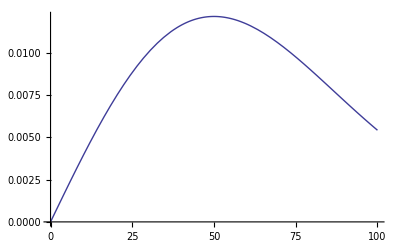

```mathematica
Plot[PDF[RayleighDistribution[50],x],{x,0,100}]
```

genData0 normalizes sums to percentages; don't use it yet:

```mathematica
genData0[label_String,range_]:=
Module[{
nums,
sum,
candidate,
normal},
nums=RandomReal[RayleighDistribution[range],Length@benchSchema];
sum=Plus@@nums;
normal=If[sum>100,nums/(sum/100),nums];
{label,zip[Append[benchSchema,"sum"],Append[normal, Plus@@normal]]}];
```

Instead, make up an association (a name-value pair) containing some data and a label (i.e., a name or tag)

```mathematica
genData[label_String,mode_,schema_:benchSchema]:={
label,
zip[
schema,
RandomReal[
RayleighDistribution[mode],
Length@schema]]};
```

```mathematica
genCluster[label_String,kinds_:memoryTypeSchema,modes_:erzatsMissRateModes,schema_:benchSchema]:={
label,
MapThread[
genData[#1,#2,schema]&,
{kinds,modes}]};
```

The following is the shape most convenient for generating this data (generates all the bottom-level data off the same parallel distributions). Pivot it for generating our charts.

```mathematica
genCluster[#,Characters["WXYZ"],RandomInteger[{1,100},4],Characters["pqrst"]]&/@Characters["abc"];
```

```mathematica
(data1=genCluster/@cacheTypeSchema)
```

(Private Caches | (Stubs | (ammp | 23.407
applu | 13.9128
apsi | 25.0763
art | 18.2925
equake | 56.9115)
Hashtables | (ammp | 18.7134
applu | 16.7704
apsi | 16.1965
art | 24.9799
equake | 17.2717)
Traces | (ammp | 9.67571
applu | 40.7501
apsi | 13.5693
art | 21.8803
equake | 23.2242)
Basic Blocks | (ammp | 10.4503
applu | 2.19866
apsi | 1.31678
art | 5.36894
equake | 5.1002))
Shared Caches | (Stubs | (ammp | 23.0109
applu | 30.4796
apsi | 24.7857
art | 41.1085
equake | 15.9159)
Hashtables | (ammp | 19.2741
applu | 20.8958
apsi | 26.5855
art | 35.8814
equake | 29.882)
Traces | (ammp | 8.3911
applu | 14.8709
apsi | 14.1976
art | 23.3585
equake | 5.96065)
Basic Blocks | (ammp | 13.6732
applu | 7.25875
apsi | 11.9421
art | 4.45489
equake | 3.98433))
Persistent Caches | (Stubs | (ammp | 52.6835
applu | 27.9305
apsi | 40.025
art | 35.4933
equake | 24.6817)
Hashtables | (ammp | 50.7071
applu | 40.1858
apsi | 56.6096
art | 35.7504
equake | 32.8409)
Traces | (ammp | 31.9585
applu | 9.96169
apsi | 18.8427
art | 8.56435
equake | 12.8407)
Basic Blocks | (ammp | 7.21299
applu | 3.87615
apsi | 2.74599
art | 8.33258
equake | 4.13775)))

Pivoting

```mathematica
Remove[pullbackNyms,extrudeNyms,pivot];
```

pullbackNyms takes a single attribute, i.e., name-value pair), whose value part is a list of other attributes, and switches the top-level name with the second-level names, and fans them out, creating an association list:

### pullbackNyms (attributeWhoseValuePartIsAnAssociationList)

```mathematica
pullbackNyms[attribute_List]:=
Module[{mNym,series},(* one attribute, i.e., name-value pair *)
{mNym,series}=attribute;
Map[
Module[{sNym,datum},
{sNym,datum}=#;
{sNym,{{mNym,datum}}}]&,
series]];
```

Test data:

```mathematica
data1⟦1,2,1⟧//TableForm
```

Stubs |  |  |  | 
ammp
23.407 | applu
13.9128 | apsi
25.0763 | art
18.2925 | equake
56.9115

Calling pullbackNyms on it:

```mathematica
pullbackNyms@data1⟦1,2,1⟧//TableForm
```

ammp | Stubs | 23.407
applu | Stubs | 13.9128
apsi | Stubs | 25.0763
art | Stubs | 18.2925
equake | Stubs | 56.9115

#### Sidebar: Another travesty generator

```mathematica
genMat[nrows_Integer,ncolumns_Integer]:=
Table[
{"R"<>ToString@i,
Table[
{"C"<>ToString@j,10*i+j},
{j,ncolumns}]},
{i,nrows}]
```

```mathematica
genMat[1,2]
```

(R1 | (C1 | 11
C2 | 12))

Calling pullbackNyms on it:

```mathematica
pullbackNyms@genMat[1,2]⟦1⟧
```

(C1 | (R1 | 11)
C2 | (R1 | 12))

Mapping pullbackNyms over all the first-level value parts:

```mathematica
pullbackNyms/@genMat[2,2]
```

({C1,(R1 | 11)} | {C2,(R1 | 12)}
{C1,(R2 | 21)} | {C2,(R2 | 22)})

### extrudeNyms

extrudeNyms is an associative, binary function that takes a pair of association lists. For each association in the first list, it looks up the corresponding value in the second list and coalesces the two values under the same name.

```mathematica
extrudeNyms[{},ll_]:=ll;
extrudeNyms[ll1_List,ll2_List]:=
Map[
Module[{mNym,v1},
{mNym,v1}=#;
{mNym,Join[v1,lookup[ll2,mNym]]}]&,
ll1];
```

Two "pulledback rows" from the original data:

```mathematica
{pullbackNyms@data1⟦1,2,1⟧,pullbackNyms@data1⟦1,2,2⟧}//TableForm
```

ammp
Stubs
23.407 | applu
Stubs
13.9128 | apsi
Stubs
25.0763 | art
Stubs
18.2925 | equake
Stubs
56.9115
ammp
Hashtables
18.7134 | applu
Hashtables
16.7704 | apsi
Hashtables
16.1965 | art
Hashtables
24.9799 | equake
Hashtables
17.2717

Extruding or coallescing on the common names:

```mathematica
extrudeNyms[pullbackNyms@data1⟦1,2,1⟧,pullbackNyms@data1⟦1,2,2⟧]//TableForm
```

ammp | Stubs | 23.407
Hashtables | 18.7134
applu | Stubs | 13.9128
Hashtables | 16.7704
apsi | Stubs | 25.0763
Hashtables | 16.1965
art | Stubs | 18.2925
Hashtables | 24.9799
equake | Stubs | 56.9115
Hashtables | 17.2717

ExtrudeNyms doesn' t care whether the later lists are permuted, defective, or superfluous in contents :

```mathematica
List[pullbackNyms@data1⟦1,2,1⟧,
RandomSample[pullbackNyms@data1⟦1,2,2⟧]]//TableForm
```

ammp
Stubs
23.407 | applu
Stubs
13.9128 | apsi
Stubs
25.0763 | art
Stubs
18.2925 | equake
Stubs
56.9115
apsi
Hashtables
16.1965 | ammp
Hashtables
18.7134 | equake
Hashtables
17.2717 | art
Hashtables
24.9799 | applu
Hashtables
16.7704

```mathematica
extrudeNyms[pullbackNyms@data1⟦1,2,1⟧,
RandomSample[pullbackNyms@data1⟦1,2,2⟧]]===
extrudeNyms[pullbackNyms@data1⟦1,2,1⟧,
pullbackNyms@data1⟦1,2,2⟧]
```

True

### pivot

Folding extrudeNyms over a map of pullbackNyms, then, is a pivot

```mathematica
pivot[twoLevel_List]:=Fold[extrudeNyms,{},pullbackNyms/@twoLevel];
```

Pivot "cluster" values one level down in a three-level hierarchy and zip them back up with their names:

```mathematica
pivot1[threeLevel_List]:=
zip[
First/@threeLevel,
pivot[Second@#]&/@threeLevel];
```

```mathematica
(data2=pivot1@data1)
```

(Private Caches | (ammp | (Stubs | 23.407
Hashtables | 18.7134
Traces | 9.67571
Basic Blocks | 10.4503)
applu | (Stubs | 13.9128
Hashtables | 16.7704
Traces | 40.7501
Basic Blocks | 2.19866)
apsi | (Stubs | 25.0763
Hashtables | 16.1965
Traces | 13.5693
Basic Blocks | 1.31678)
art | (Stubs | 18.2925
Hashtables | 24.9799
Traces | 21.8803
Basic Blocks | 5.36894)
equake | (Stubs | 56.9115
Hashtables | 17.2717
Traces | 23.2242
Basic Blocks | 5.1002))
Shared Caches | (ammp | (Stubs | 23.0109
Hashtables | 19.2741
Traces | 8.3911
Basic Blocks | 13.6732)
applu | (Stubs | 30.4796
Hashtables | 20.8958
Traces | 14.8709
Basic Blocks | 7.25875)
apsi | (Stubs | 24.7857
Hashtables | 26.5855
Traces | 14.1976
Basic Blocks | 11.9421)
art | (Stubs | 41.1085
Hashtables | 35.8814
Traces | 23.3585
Basic Blocks | 4.45489)
equake | (Stubs | 15.9159
Hashtables | 29.882
Traces | 5.96065
Basic Blocks | 3.98433))
Persistent Caches | (ammp | (Stubs | 52.6835
Hashtables | 50.7071
Traces | 31.9585
Basic Blocks | 7.21299)
applu | (Stubs | 27.9305
Hashtables | 40.1858
Traces | 9.96169
Basic Blocks | 3.87615)
apsi | (Stubs | 40.025
Hashtables | 56.6096
Traces | 18.8427
Basic Blocks | 2.74599)
art | (Stubs | 35.4933
Hashtables | 35.7504
Traces | 8.56435
Basic Blocks | 8.33258)
equake | (Stubs | 24.6817
Hashtables | 32.8409
Traces | 12.8407
Basic Blocks | 4.13775)))

```mathematica
data2//InputForm
```

{{"Private Caches", {{"ammp", {{"Stubs", 23.406989368291377}, 
     {"Hashtables", 18.7134058689657}, 
     {"Traces", 9.675706007491652}, {"Basic Blocks", 
      10.450329223019262}}}, {"applu", 
    {{"Stubs", 13.91284096640738}, {"Hashtables", 
      16.770356980139752}, {"Traces", 40.75009887596629}, 
     {"Basic Blocks", 2.198661794858368}}}, 
   {"apsi", {{"Stubs", 25.076348688382716}, 
     {"Hashtables", 16.1965392092989}, 
     {"Traces", 13.56932082338863}, {"Basic Blocks", 
      1.3167831269790486}}}, {"art", {{"Stubs", 18.29245295816367}, 
     {"Hashtables", 24.979876534973766}, 
     {"Traces", 21.880257505292285}, {"Basic Blocks", 
      5.3689364864379785}}}, {"equake", 
    {{"Stubs", 56.911466279250234}, {"Hashtables", 
      17.271674349016422}, {"Traces", 23.2241865390702}, 
     {"Basic Blocks", 5.100199743366839}}}}}, 
 {"Shared Caches", {{"ammp", {{"Stubs", 23.01093571856974}, 
     {"Hashtables", 19.27411813399193}, 
     {"Traces", 8.391100619135141}, {"Basic Blocks", 
      13.673192487958474}}}, {"applu", 
    {{"Stubs", 30.479615401267434}, {"Hashtables", 
      20.895786583546883}, {"Traces", 14.870863372893863}, 
     {"Basic Blocks", 7.2587452086805895}}}, 
   {"apsi", {{"Stubs", 24.785668128321724}, 
     {"Hashtables", 26.585512440930344}, 
     {"Traces", 14.197582987939832}, {"Basic Blocks", 
      11.942082821413454}}}, 
   {"art", {{"Stubs", 41.108488572639864}, {"Hashtables", 
      35.881429419152155}, {"Traces", 23.3584955136164}, 
     {"Basic Blocks", 4.45489238990611}}}, 
   {"equake", {{"Stubs", 15.915916052160078}, 
     {"Hashtables", 29.882025595737687}, 
     {"Traces", 5.9606505853498755}, {"Basic Blocks", 
      3.984329088236185}}}}}, {"Persistent Caches", 
  {{"ammp", {{"Stubs", 52.68352670064205}, {"Hashtables", 
      50.70709015806181}, {"Traces", 31.958504462470252}, 
     {"Basic Blocks", 7.212987954453096}}}, 
   {"applu", {{"Stubs", 27.930530516741143}, 
     {"Hashtables", 40.185842885787515}, 
     {"Traces", 9.961685928076067}, {"Basic Blocks", 
      3.876150878579314}}}, {"apsi", {{"Stubs", 40.02498346320697}, 
     {"Hashtables", 56.60961967755658}, 
     {"Traces", 18.842709992019298}, {"Basic Blocks", 
      2.745985983439465}}}, {"art", {{"Stubs", 35.49329404338298}, 
     {"Hashtables", 35.75039987085724}, 
     {"Traces", 8.564346797309542}, {"Basic Blocks", 
      8.332579244097873}}}, {"equake", 
    {{"Stubs", 24.68174006384305}, {"Hashtables", 
      32.840901903459745}, {"Traces", 12.84069406770326}, 
     {"Basic Blocks", 4.137750537285277}}}}}}

This round-trips, of course:

```mathematica
pivot1@data2===data1
```

True

Quick-and-Dirty Chart

One of the three clusters:

```mathematica
data2⟦1,2⟧
```

(ammp | (Stubs | 23.407
Hashtables | 18.7134
Traces | 9.67571
Basic Blocks | 10.4503)
applu | (Stubs | 13.9128
Hashtables | 16.7704
Traces | 40.7501
Basic Blocks | 2.19866)
apsi | (Stubs | 25.0763
Hashtables | 16.1965
Traces | 13.5693
Basic Blocks | 1.31678)
art | (Stubs | 18.2925
Hashtables | 24.9799
Traces | 21.8803
Basic Blocks | 5.36894)
equake | (Stubs | 56.9115
Hashtables | 17.2717
Traces | 23.2242
Basic Blocks | 5.1002))

Pick the pieces to display:

```mathematica
(Second/@data2⟦1,2⟧)//TableForm
```

Stubs
23.407 | Hashtables
18.7134 | Traces
9.67571 | Basic Blocks
10.4503
Stubs
13.9128 | Hashtables
16.7704 | Traces
40.7501 | Basic Blocks
2.19866
Stubs
25.0763 | Hashtables
16.1965 | Traces
13.5693 | Basic Blocks
1.31678
Stubs
18.2925 | Hashtables
24.9799 | Traces
21.8803 | Basic Blocks
5.36894
Stubs
56.9115 | Hashtables
17.2717 | Traces
23.2242 | Basic Blocks
5.1002

Strip off the labels for now:

```mathematica
cluster1=
Reverse/@
((Second/@#)&/@ (* skip the labels *)
(Second/@data2⟦1,2⟧))
```

(10.4503 | 9.67571 | 18.7134 | 23.407
2.19866 | 40.7501 | 16.7704 | 13.9128
1.31678 | 13.5693 | 16.1965 | 25.0763
5.36894 | 21.8803 | 24.9799 | 18.2925
5.1002 | 23.2242 | 17.2717 | 56.9115)

Making no attempt at this time to normalize stacks to 100 (percent).

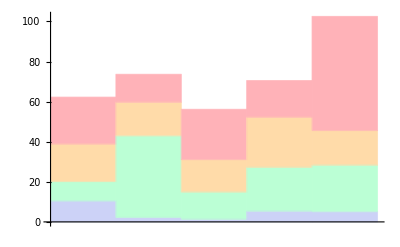

```mathematica
BarChart[
cluster1,
ChartLayout->"Stacked",
BarSpacing->{0,0}]
```

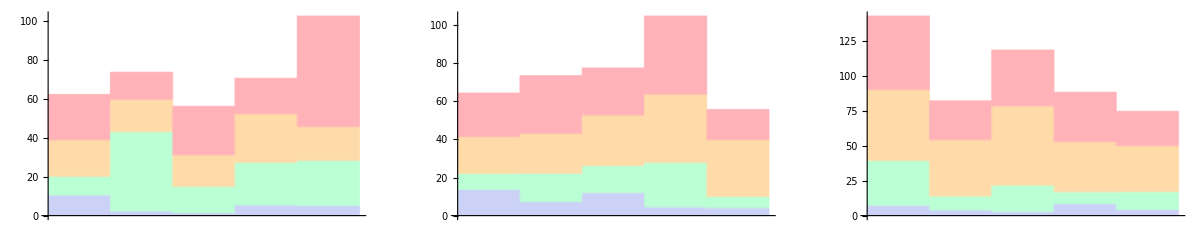

```mathematica
GraphicsRow[
BarChart[
Reverse/@
((Second/@#)&/@ (* skip the labels *)
(Second/@Second[#])),
ChartLayout->"Stacked",
BarSpacing->{0,0}]&/@
data2,
AspectRatio->1]
```

Data-Series Properties and Behaviors:

### Enumerating the Contained Data

"... data series knows how to enumerate the data ..."

It takes 6 indices to hit paydirt on the data above:

```mathematica
Depth@data2
```

7

They come in pairs, {x, 2}, the x to get a certain element, 2 to get the values instead of the labels:

```mathematica
data2⟦1⟧⟦2⟧⟦1⟧⟦2⟧⟦1⟧⟦2⟧
```

23.407

```mathematica
flattenedData=Flatten[
Table[
{"/"<>data2⟦i⟧⟦1⟧<>
"/"<>data2⟦i⟧⟦2⟧⟦j⟧⟦1⟧<>
"/"<>data2⟦i⟧⟦2⟧⟦j⟧⟦2⟧⟦k⟧⟦1⟧,
data2⟦i⟧⟦2⟧⟦j⟧⟦2⟧⟦k⟧⟦2⟧},
{i,Length@data2},
{j,Length@data2⟦1⟧⟦2⟧},
{k,Length@data2⟦1⟧⟦2⟧⟦1⟧⟦2⟧}],
2]
```

(/Private Caches/ammp/Stubs | 23.407
/Private Caches/ammp/Hashtables | 18.7134
/Private Caches/ammp/Traces | 9.67571
/Private Caches/ammp/Basic Blocks | 10.4503
/Private Caches/applu/Stubs | 13.9128
/Private Caches/applu/Hashtables | 16.7704
/Private Caches/applu/Traces | 40.7501
/Private Caches/applu/Basic Blocks | 2.19866
/Private Caches/apsi/Stubs | 25.0763
/Private Caches/apsi/Hashtables | 16.1965
/Private Caches/apsi/Traces | 13.5693
/Private Caches/apsi/Basic Blocks | 1.31678
/Private Caches/art/Stubs | 18.2925
/Private Caches/art/Hashtables | 24.9799
/Private Caches/art/Traces | 21.8803
/Private Caches/art/Basic Blocks | 5.36894
/Private Caches/equake/Stubs | 56.9115
/Private Caches/equake/Hashtables | 17.2717
/Private Caches/equake/Traces | 23.2242
/Private Caches/equake/Basic Blocks | 5.1002
/Shared Caches/ammp/Stubs | 23.0109
/Shared Caches/ammp/Hashtables | 19.2741
/Shared Caches/ammp/Traces | 8.3911
/Shared Caches/ammp/Basic Blocks | 13.6732
/Shared Caches/applu/Stubs | 30.4796
/Shared Caches/applu/Hashtables | 20.8958
/Shared Caches/applu/Traces | 14.8709
/Shared Caches/applu/Basic Blocks | 7.25875
/Shared Caches/apsi/Stubs | 24.7857
/Shared Caches/apsi/Hashtables | 26.5855
/Shared Caches/apsi/Traces | 14.1976
/Shared Caches/apsi/Basic Blocks | 11.9421
/Shared Caches/art/Stubs | 41.1085
/Shared Caches/art/Hashtables | 35.8814
/Shared Caches/art/Traces | 23.3585
/Shared Caches/art/Basic Blocks | 4.45489
/Shared Caches/equake/Stubs | 15.9159
/Shared Caches/equake/Hashtables | 29.882
/Shared Caches/equake/Traces | 5.96065
/Shared Caches/equake/Basic Blocks | 3.98433
/Persistent Caches/ammp/Stubs | 52.6835
/Persistent Caches/ammp/Hashtables | 50.7071
/Persistent Caches/ammp/Traces | 31.9585
/Persistent Caches/ammp/Basic Blocks | 7.21299
/Persistent Caches/applu/Stubs | 27.9305
/Persistent Caches/applu/Hashtables | 40.1858
/Persistent Caches/applu/Traces | 9.96169
/Persistent Caches/applu/Basic Blocks | 3.87615
/Persistent Caches/apsi/Stubs | 40.025
/Persistent Caches/apsi/Hashtables | 56.6096
/Persistent Caches/apsi/Traces | 18.8427
/Persistent Caches/apsi/Basic Blocks | 2.74599
/Persistent Caches/art/Stubs | 35.4933
/Persistent Caches/art/Hashtables | 35.7504
/Persistent Caches/art/Traces | 8.56435
/Persistent Caches/art/Basic Blocks | 8.33258
/Persistent Caches/equake/Stubs | 24.6817
/Persistent Caches/equake/Hashtables | 32.8409
/Persistent Caches/equake/Traces | 12.8407
/Persistent Caches/equake/Basic Blocks | 4.13775)

A generic problem here is to generate similar expressions for hierarchies of arbitrary depth. This will have a nice recursive solution.

For defining this enumerator, a tree is either a list of tree nodes or is a numeric value. A tree node is an association of a name with a subtree.

This is a tree because it's a list containing a single tree node, which is an association of a name with a subtree. That subtree is a numeric value.

```mathematica
{{"a",1}}
```

(a | 1)

It's also just an ordinary association list.

```mathematica
isAl@{{"a",1}}
```

True

Thre predicate "isTree" embodies the definition

```mathematica
Remove[isTree];
isTree[v_?NumberQ]:=True;
isTree[l_?isAl]:=And@@(Composition[isTree,Second]/@l);
isTree[xs___]=False;
```

```mathematica
isTree@{{"a",1}}
```

True

Here's a tree containing one tree node whose name is "x" and whose subtree is the list of tree nodes {{"a", 1}, {"b", 2}}

```mathematica
isTree@{{"x",{{"a",1},{"b",2}}}}
```

True

A "dimensional hierarchy" is one in which all subtrees at a given level have the same structure, meaning the same names, recursively, though not necessarily the same values. (The term is borrowed from OLAP, and is not consistent with ordinary mathematical definitions of "dimension.")

```mathematica
isTree@
{{"x",{{"a",1},{"b",2}}},
{"y",{{"a",3},{"b",4}}}}
```

True

```mathematica
isTree@
{{"p",{
{"x",{{"a",1},{"b",2}}},
{"y",{{"a",3},{"b",4}}}}},
{"q",{
{"x",{{"a",5},{"b",6}}},
{"y",{{"a",7},{"b",8}}}}},
{"r",{
{"x",{{"a",9},{"b",10}}},
{"y",{{"a",11},{"b",12}}}}}}
```

True

### treeToPathedEnumerable

Here's a function that translates a tree into a linear association list, each of whose names is a path expression made up by concatenating the names (with / prefixes) along the arc to leaf values. This kind of path expression is just like a file path in a disk directory.

```mathematica
Remove[treeToPathedEnumerable];
treeToPathedEnumerable[{}]={};
treeToPathedEnumerable[v_?NumberQ]:=v;
treeToPathedEnumerable[{{n_String,v_?NumberQ},ns___}]:=
Join[
{{"/"<>n,v}},
treeToPathedEnumerable@{ns}];
treeToPathedEnumerable[{{n_String,v_List},ns___}]:=
Join[
Map[
Function[node,
Module[{dn,dv},
{dn,dv}=node;
{"/"<>n<>dn,treeToPathedEnumerable@dv}]],
treeToPathedEnumerable@v],
treeToPathedEnumerable@{ns}];
```

```mathematica
treeToPathedEnumerable@{{"a",1}}
```

(/a | 1)

```mathematica
treeToPathedEnumerable@
{{"x",{{"a",1},{"b",2}}},
{"y",{{"a",3},{"b",4}}}}
```

(/x/a | 1
/x/b | 2
/y/a | 3
/y/b | 4)

```mathematica
dTestTree=genCluster[
#,
Characters["xy"],
RandomInteger[{1,100},2],
Characters["ab"]]&/@
Characters["pqr"]
```

(p | (x | (a | 78.8271
b | 78.8732)
y | (a | 87.0298
b | 74.0255))
q | (x | (a | 180.177
b | 218.854)
y | (a | 16.3088
b | 16.1965))
r | (x | (a | 122.789
b | 131.436)
y | (a | 218.295
b | 235.015)))

```mathematica
treeToPathedEnumerable@dTestTree
```

(/p/x/a | 78.8271
/p/x/b | 78.8732
/p/y/a | 87.0298
/p/y/b | 74.0255
/q/x/a | 180.177
/q/x/b | 218.854
/q/y/a | 16.3088
/q/y/b | 16.1965
/r/x/a | 122.789
/r/x/b | 131.436
/r/y/a | 218.295
/r/y/b | 235.015)

It works on non - dimensional trees, too :

```mathematica
isTree@
(ndTestTree=
{{"p",{
{"x",{{"a",1},{"b",2},{"c",{{"d",42}}}}},
{"y",{{"a",3},{"b",4}}}}},
{"q",29},
{"r",{
{"x",9},
{"y",{{"a",11},{"b",12}}}}}})
```

True

```mathematica
treeToPathedEnumerable@ndTestTree
```

(/p/x/a | 1
/p/x/b | 2
/p/x/c/d | 42
/p/y/a | 3
/p/y/b | 4
/q | 29
/r/x | 9
/r/y/a | 11
/r/y/b | 12)

It works on our actual dimensional hierarchy:

```mathematica
treeToPathedEnumerable[data2]===flattenedData
```

True

Finally Data Series

### Data Range

```mathematica
dataRange[aList_?isAl]:=
{Min@@(Second/@aList),Max@@(Second/@aList)}
```

```mathematica
dataRange@flattenedData
```

{1.31678,56.9115}

### Constructor

```mathematica
Remove[newDataSeries];
newDataSeries[rawData_?NumberQ, name_:Unique[]]:=
{{"$type","DataSeries"},
{"dataSeriesType","single value"}, 
{"name",name},
{"rawData",rawData},
{"enumerable",List[rawData]},
{"rawEnumerable",List[rawData]},
{"range",List[rawData,rawData]}};
newDataSeries[rawData_List:{},name_:Unique[]]:=
Module[{pathed,rawEnum,range},
pathed=treeToPathedEnumerable[rawData];
rawEnum=Second/@pathed;
range=List[Min@@rawEnum,Max@@rawEnum];
{{"$type","DataSeries"},
{"dataSeriesType","dimensional hierarchy"}, (* the only list type for now *)
{"name",name},
{"rawData",rawData},
{"enumerable",pathed},
{"rawEnumerable",rawEnum},
{"range",range}}];
```

```mathematica
newDataSeries[7]
```

($type | DataSeries
dataSeriesType | single value
name | $60
rawData | 7
enumerable | {7}
rawEnumerable | {7}
range | {7,7})

```mathematica
newDataSeries[]
```

($type | DataSeries
dataSeriesType | dimensional hierarchy
name | $61
rawData | {}
enumerable | {}
rawEnumerable | {}
range | {∞,-∞})

```mathematica
newDataSeries[dTestTree,"foo"]
```

($type | DataSeries
dataSeriesType | dimensional hierarchy
name | foo
rawData | (p | (x | (a | 78.8271
b | 78.8732)
y | (a | 87.0298
b | 74.0255))
q | (x | (a | 180.177
b | 218.854)
y | (a | 16.3088
b | 16.1965))
r | (x | (a | 122.789
b | 131.436)
y | (a | 218.295
b | 235.015)))
enumerable | (/p/x/a | 78.8271
/p/x/b | 78.8732
/p/y/a | 87.0298
/p/y/b | 74.0255
/q/x/a | 180.177
/q/x/b | 218.854
/q/y/a | 16.3088
/q/y/b | 16.1965
/r/x/a | 122.789
/r/x/b | 131.436
/r/y/a | 218.295
/r/y/b | 235.015)
rawEnumerable | {78.8271,78.8732,87.0298,74.0255,180.177,218.854,16.3088,16.1965,122.789,131.436,218.295,235.015}
range | {16.1965,235.015})

### Predicates

```mathematica
IsDataSeries[candidate_]:=Is[candidate,"DataSeries"];
```

```mathematica
ds1=newDataSeries[data2];
```

```mathematica
GetType[ds1]
```

DataSeries

```mathematica
IsDataSeries[ds1]
```

True

### Accessors

#### Enumerating sub-DataSeries

Given a data series, return a list of sub Data Series

```mathematica
subDataSeries[ds_?IsDataSeries]:=subDataSeriesα[lookup[ds,"rawData"]];
```

```mathematica
subDataSeriesα[data_?NumberQ]:={};
subDataSeriesα[data_List]:=
Map[
Function[treeNode,
newDataSeries[Second@treeNode,First@treeNode]],
data];
```

```mathematica
subDataSeries[newDataSeries[data2]]//TableForm
```

$type
DataSeries | dataSeriesType
dimensional hierarchy | name
Private Caches | rawData |  |  |  | 
ammp |  |  | 
Stubs
23.407 | Hashtables
18.7134 | Traces
9.67571 | Basic Blocks
10.4503 | applu |  |  | 
Stubs
13.9128 | Hashtables
16.7704 | Traces
40.7501 | Basic Blocks
2.19866 | apsi |  |  | 
Stubs
25.0763 | Hashtables
16.1965 | Traces
13.5693 | Basic Blocks
1.31678 | art |  |  | 
Stubs
18.2925 | Hashtables
24.9799 | Traces
21.8803 | Basic Blocks
5.36894 | equake |  |  | 
Stubs
56.9115 | Hashtables
17.2717 | Traces
23.2242 | Basic Blocks
5.1002 | enumerable |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
/ammp/Stubs
23.407 | /ammp/Hashtables
18.7134 | /ammp/Traces
9.67571 | /ammp/Basic Blocks
10.4503 | /applu/Stubs
13.9128 | /applu/Hashtables
16.7704 | /applu/Traces
40.7501 | /applu/Basic Blocks
2.19866 | /apsi/Stubs
25.0763 | /apsi/Hashtables
16.1965 | /apsi/Traces
13.5693 | /apsi/Basic Blocks
1.31678 | /art/Stubs
18.2925 | /art/Hashtables
24.9799 | /art/Traces
21.8803 | /art/Basic Blocks
5.36894 | /equake/Stubs
56.9115 | /equake/Hashtables
17.2717 | /equake/Traces
23.2242 | /equake/Basic Blocks
5.1002 | rawEnumerable |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
23.407 | 18.7134 | 9.67571 | 10.4503 | 13.9128 | 16.7704 | 40.7501 | 2.19866 | 25.0763 | 16.1965 | 13.5693 | 1.31678 | 18.2925 | 24.9799 | 21.8803 | 5.36894 | 56.9115 | 17.2717 | 23.2242 | 5.1002 | range | 
1.31678 | 56.9115
$type
DataSeries | dataSeriesType
dimensional hierarchy | name
Shared Caches | rawData |  |  |  | 
ammp |  |  | 
Stubs
23.0109 | Hashtables
19.2741 | Traces
8.3911 | Basic Blocks
13.6732 | applu |  |  | 
Stubs
30.4796 | Hashtables
20.8958 | Traces
14.8709 | Basic Blocks
7.25875 | apsi |  |  | 
Stubs
24.7857 | Hashtables
26.5855 | Traces
14.1976 | Basic Blocks
11.9421 | art |  |  | 
Stubs
41.1085 | Hashtables
35.8814 | Traces
23.3585 | Basic Blocks
4.45489 | equake |  |  | 
Stubs
15.9159 | Hashtables
29.882 | Traces
5.96065 | Basic Blocks
3.98433 | enumerable |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
/ammp/Stubs
23.0109 | /ammp/Hashtables
19.2741 | /ammp/Traces
8.3911 | /ammp/Basic Blocks
13.6732 | /applu/Stubs
30.4796 | /applu/Hashtables
20.8958 | /applu/Traces
14.8709 | /applu/Basic Blocks
7.25875 | /apsi/Stubs
24.7857 | /apsi/Hashtables
26.5855 | /apsi/Traces
14.1976 | /apsi/Basic Blocks
11.9421 | /art/Stubs
41.1085 | /art/Hashtables
35.8814 | /art/Traces
23.3585 | /art/Basic Blocks
4.45489 | /equake/Stubs
15.9159 | /equake/Hashtables
29.882 | /equake/Traces
5.96065 | /equake/Basic Blocks
3.98433 | rawEnumerable |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
23.0109 | 19.2741 | 8.3911 | 13.6732 | 30.4796 | 20.8958 | 14.8709 | 7.25875 | 24.7857 | 26.5855 | 14.1976 | 11.9421 | 41.1085 | 35.8814 | 23.3585 | 4.45489 | 15.9159 | 29.882 | 5.96065 | 3.98433 | range | 
3.98433 | 41.1085
$type
DataSeries | dataSeriesType
dimensional hierarchy | name
Persistent Caches | rawData |  |  |  | 
ammp |  |  | 
Stubs
52.6835 | Hashtables
50.7071 | Traces
31.9585 | Basic Blocks
7.21299 | applu |  |  | 
Stubs
27.9305 | Hashtables
40.1858 | Traces
9.96169 | Basic Blocks
3.87615 | apsi |  |  | 
Stubs
40.025 | Hashtables
56.6096 | Traces
18.8427 | Basic Blocks
2.74599 | art |  |  | 
Stubs
35.4933 | Hashtables
35.7504 | Traces
8.56435 | Basic Blocks
8.33258 | equake |  |  | 
Stubs
24.6817 | Hashtables
32.8409 | Traces
12.8407 | Basic Blocks
4.13775 | enumerable |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
/ammp/Stubs
52.6835 | /ammp/Hashtables
50.7071 | /ammp/Traces
31.9585 | /ammp/Basic Blocks
7.21299 | /applu/Stubs
27.9305 | /applu/Hashtables
40.1858 | /applu/Traces
9.96169 | /applu/Basic Blocks
3.87615 | /apsi/Stubs
40.025 | /apsi/Hashtables
56.6096 | /apsi/Traces
18.8427 | /apsi/Basic Blocks
2.74599 | /art/Stubs
35.4933 | /art/Hashtables
35.7504 | /art/Traces
8.56435 | /art/Basic Blocks
8.33258 | /equake/Stubs
24.6817 | /equake/Hashtables
32.8409 | /equake/Traces
12.8407 | /equake/Basic Blocks
4.13775 | rawEnumerable |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
52.6835 | 50.7071 | 31.9585 | 7.21299 | 27.9305 | 40.1858 | 9.96169 | 3.87615 | 40.025 | 56.6096 | 18.8427 | 2.74599 | 35.4933 | 35.7504 | 8.56435 | 8.33258 | 24.6817 | 32.8409 | 12.8407 | 4.13775 | range | 
2.74599 | 56.6096

```mathematica
subDataSeries[
subDataSeries[
newDataSeries[data2]]⟦1⟧]//TableForm
```

$type
DataSeries | dataSeriesType
dimensional hierarchy | name
ammp | rawData |  |  | 
Stubs
23.407 | Hashtables
18.7134 | Traces
9.67571 | Basic Blocks
10.4503 | enumerable |  |  | 
/Stubs
23.407 | /Hashtables
18.7134 | /Traces
9.67571 | /Basic Blocks
10.4503 | rawEnumerable |  |  | 
23.407 | 18.7134 | 9.67571 | 10.4503 | range | 
9.67571 | 23.407
$type
DataSeries | dataSeriesType
dimensional hierarchy | name
applu | rawData |  |  | 
Stubs
13.9128 | Hashtables
16.7704 | Traces
40.7501 | Basic Blocks
2.19866 | enumerable |  |  | 
/Stubs
13.9128 | /Hashtables
16.7704 | /Traces
40.7501 | /Basic Blocks
2.19866 | rawEnumerable |  |  | 
13.9128 | 16.7704 | 40.7501 | 2.19866 | range | 
2.19866 | 40.7501
$type
DataSeries | dataSeriesType
dimensional hierarchy | name
apsi | rawData |  |  | 
Stubs
25.0763 | Hashtables
16.1965 | Traces
13.5693 | Basic Blocks
1.31678 | enumerable |  |  | 
/Stubs
25.0763 | /Hashtables
16.1965 | /Traces
13.5693 | /Basic Blocks
1.31678 | rawEnumerable |  |  | 
25.0763 | 16.1965 | 13.5693 | 1.31678 | range | 
1.31678 | 25.0763
$type
DataSeries | dataSeriesType
dimensional hierarchy | name
art | rawData |  |  | 
Stubs
18.2925 | Hashtables
24.9799 | Traces
21.8803 | Basic Blocks
5.36894 | enumerable |  |  | 
/Stubs
18.2925 | /Hashtables
24.9799 | /Traces
21.8803 | /Basic Blocks
5.36894 | rawEnumerable |  |  | 
18.2925 | 24.9799 | 21.8803 | 5.36894 | range | 
5.36894 | 24.9799
$type
DataSeries | dataSeriesType
dimensional hierarchy | name
equake | rawData |  |  | 
Stubs
56.9115 | Hashtables
17.2717 | Traces
23.2242 | Basic Blocks
5.1002 | enumerable |  |  | 
/Stubs
56.9115 | /Hashtables
17.2717 | /Traces
23.2242 | /Basic Blocks
5.1002 | rawEnumerable |  |  | 
56.9115 | 17.2717 | 23.2242 | 5.1002 | range | 
5.1002 | 56.9115

Need an analogue of "Part" for these data series:

```mathematica
(stackDs001001=
subDataSeries[
subDataSeries[
newDataSeries[data2]]⟦1⟧]⟦1⟧)//TableForm
```

$type | DataSeries
dataSeriesType | dimensional hierarchy
name | ammp
rawData | Stubs | 23.407
Hashtables | 18.7134
Traces | 9.67571
Basic Blocks | 10.4503
enumerable | /Stubs | 23.407
/Hashtables | 18.7134
/Traces | 9.67571
/Basic Blocks | 10.4503
rawEnumerable | 23.407
18.7134
9.67571
10.4503
range | 9.67571
23.407

## Shape

[Shape] -- (1) canonical shape (point, bar, prism, bubble, surface patch, jpg, blob, label; (2) result of geometry construction, populated with data series and other shapes; metadata = inputs for BinderArrangers and hints for LayoutHelpers, rectilinear/curvilinear, planar/volume-occupying, symmetries, textual, colored/texturable
	A geometry can construct a list, graph, or tree of shapes, so this must, recursively, also be considered a Shape. That fact is built-in to our current model for shapes.

```mathematica
GetType@newRp[]
```

rectangularPrism

```mathematica
newRp[]
```

(bounds | (height | 1
width | 1
depth | 1)
localTf | TransformationFunction[(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)]
children | {}
$type | rectangularPrism)

```mathematica
newShape[]:=
{{"children",{}},
{"localTf", TfIdentity[3]},
{"$type","Shape"}};
```

```mathematica
new2DShape[]:=
{{"children",{}},
{"localTf", TfIdentity[2]},
{"$type","2DShape"}};
```

Here's where we could use general "inheritance," but just code the list of admissable subtypes explicitly for this special case.

```mathematica
IsShape[candidate_]:=
Is[candidate,"Shape"]||
Is[candidate,"2DShape"]||
Is[candidate,"ShapeList"]||
Is[candidate,"rectangularPrism"]||
Is[candidate,"2DRectangle"];
```

```mathematica
IsShapes[shapes_List]:=
And@@(IsShape/@shapes)
```

```mathematica
newShape[l_?IsShapes,ltf_: TfIdentity[3]]:=
{{"children",l},
{"localTf", ltf},
{"$type","ShapeList"}};
```

2DRectangle

```mathematica
new2DRectangle[]:=
{{"children",{}},
{"localTf", TfIdentity[2]},
{"color",Black},
{"bounds", {{"depth",0},{"height",1},{"width", 1}}},
{"$type", "2DRectangle"}};
```

```mathematica
new2DRectangle[]
```

(children | {}
localTf | TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]
color | GrayLevel[0]
bounds | (depth | 0
height | 1
width | 1)
$type | 2DRectangle)

## Bounds To 2DRectangle To 2DRectangle

boundsTo2DRectangleTo2DRectangle takes a bounds spec and makes a property setter that applies that bounds spec to a 2DRectangle.

Keep the bounds and the localTf consistent (not sure whether to compose or to overwrite, in general, but overwriting is safer)

```mathematica
boundsTo2DRectangleTo2DRectangle[bounds_]:=
Module[{keys={"width","depth","height"}},
Function[rp,(* can reuse some 3D things *)
Module[{newVals=boundsAndRp2Vals[bounds,rp,keys]},
adjoin[rp,
{{"bounds", MapThread[List,{keys,newVals}]},
{"localTf",ScalingTransform[
(* pick out the 2D subset *)
{newVals⟦1⟧,newVals⟦3⟧}]}}
]]]];
```

The following applies a data binding to a particular Rp, this time, a bar:

```mathematica
boundsTo2DRectangleTo2DRectangle[{{"depth",17}}]@new2DRectangle[]
```

(bounds | (width | 1
depth | 17
height | 1)
children | {}
color | GrayLevel[0]
localTf | TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]
$type | 2DRectangle)

```mathematica
boundsTo2DRectangleTo2DRectangle[{{"depth",17},{"height",29}}]@new2DRectangle[]
```

(bounds | (width | 1
depth | 17
height | 29)
children | {}
color | GrayLevel[0]
localTf | TransformationFunction[(1 | 0 | 0
0 | 29 | 0
0 | 0 | 1)]
$type | 2DRectangle)

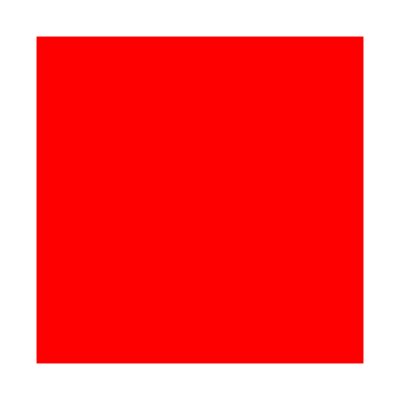

```mathematica
Graphics[{Blue,{Red,Rectangle[{0,0},{1,1}]}}]
```

```mathematica
render2DVz[new2DRectangle[]]
```

-Graphics-

## AxisSet

[Axis] -- mapping of an enumerable to anything visible, even if only indirectly: Euclidean, animation, stack position, cluster position, motion speed, color, geolocation, etc.

[AxisSet] -- visibility/hidden; scrollable; titles, labels, subdivision, granularity; range (e.g., negatives?)

```mathematica
newAxis[]:=
{{"$type","Axis"},
{"mapping",id}};
```

```mathematica
newAxisSet[axis_:newAxis[]]:=
{{"$type","AxisSet"},
{"axis",axis},
{"visible",True},
{"scrollable",False},
{"subdivision",0},
{"granularity",0},
{"range",{0,1}},
{"titles",{}}};
```

```mathematica
IsAxis=Is[#,"Axis"]&;
IsAxisSet=Is[#,"AxisSet"]&;
IsAxes=Apply[And,IsAxis/@#]&;
```

A percentage stack axis maps a list (which is an enumerable) of non-negative numbers proportionately so that they sum to 100. The geometry can apply this to shapes by recovering the absolute information from the Data Series.

```mathematica
newPercentageStackAxis[]:=
{{"$type","Axis"},
{"mapping",
Function[
list,
Module[
{s=Plus@@list},
Map[#/s&,list]]]}};
```

```mathematica
lookup[newPercentageStackAxis[],"mapping"][
lookup[stackDs001001,"rawEnumerable"]]
```

{0.376037,0.300634,0.155442,0.167886}

```mathematica
FoldList[Plus,0,
lookup[newPercentageStackAxis[],"mapping"][
lookup[stackDs001001,"rawEnumerable"]]]
```

{0,0.376037,0.676672,0.832114,1.}

## GeometryTransformer

mumble

### Two-Dimensional Transform Composers and Rewriters

```mathematica
unitScoot2D={0,0};
unitSqueeze2D={1,1};
unitTwist2D={0,{0,0}};
unitShear2D={0,{1,0},{0,1}};
unitFlip2D={};
Remove[transformComposer2D,transformCompositionPsm2D,transformRewriter2D, transformRewritePsm2D];

transformComposer2D[vz_,
scoot_:unitScoot2D,
squeeze_:unitSqueeze2D,
twist_:unitTwist2D,
shear_:unitShear2D,
flip_:unitFlip2D]:=
adjoin[vz,"localTf",
Composition[
TranslationTransform[scoot],
Apply[ShearingTransform, shear],
Apply[RotationTransform,twist],
ScalingTransform[squeeze],
lookup[vz,"localTf"]]];

transformCompositionPsm2D[
scoot_:unitScoot2D,
squeeze_:unitSqueeze2D,
twist_:unitTwist2D,
shear_:unitShear2D,
flip_:unitFlip2D]:=
Function[vz,
adjoin[vz,"localTf",
Composition[
TranslationTransform[scoot],
Apply[ShearingTransform, shear],
Apply[RotationTransform,twist],
ScalingTransform[squeeze],
lookup[vz,"localTf"]]]];

transformRewriter2D[vz_,
scoot_:unitScoot2D,
squeeze_:unitSqueeze2D,
twist_:unitTwist2D,
shear_:unitShear2D,
flip_:unitFlip2D]:=
adjoin[vz,"localTf",
Composition[
TranslationTransform[scoot],
Apply[ShearingTransform, shear],
Apply[RotationTransform,twist],
ScalingTransform[squeeze],
TfIdentity[2]]];

transformRewritePsm2D[
scoot_:unitScoot2D,
squeeze_:unitSqueeze2D,
twist_:unitTwist2D,
shear_:unitShear2D,
flip_:unitFlip2D]:=
Function[vz,
adjoin[vz,"localTf",
Composition[
TranslationTransform[scoot],
Apply[ShearingTransform, shear],
Apply[RotationTransform,twist],
ScalingTransform[squeeze],
TfIdentity[2]]]];
```

Mumble

## Geometry

[Geometry] -- mapping from DataSeries, list of shapes, axis, and binding params to another shape; has
		[Container] -- Shape into which new shapes compose; bounding box; coordinate frame; proportions; subdivision; color, texture, transparency, etc.
		[BinderArranger] -- (I believe these are a tweak on the older "Property-Setter" idea) Generates [ShapeInstanceSeries], result of applying DataSeries and input Shapes to [DataShapeBindingParams] (mapping data to dimensional or visual attributes, shape selectors from values), result of mapping input AxisSet to container's coordinate system and its other visual elements (stacking, clustering, coloring, motion); layout ShapeInstanceSeries to axes per [ShapeAxisBindingParams]; interpolate where necessary

Example: a stacker geometry takes a data series whose type is

```mathematica
changeType[newType_String]:=dtmm[newType&][{"$type"}];
```

```mathematica
changeColor[hue_?NumberQ]:=dtmm[hue&][{"color"}];
```

```mathematica
newContainer[]:=
changeType["container"][newRp[]];
```

```mathematica
newContainer[]
```

(bounds | (height | 1
width | 1
depth | 1)
localTf | TransformationFunction[(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)]
children | {}
$type | container)

The binder-arranger for the stacker geometry creates a list of copies of the input shape, the height of each of which comes from the raw enumerable of the data series piped through the mapping of the axis.

```mathematica
StackerGeometry[shape_?IsShape,ds_?IsDataSeries,axs_?IsAxisSet]:=
Module[{rawEn,axisMap,heights,feet,
nuShapes,nu2Shapes,nu3Shapes},
axisMap=lookup[lookup[axs,"axis"],"mapping"];
rawEn=lookup[ds,"rawEnumerable"];
heights=axisMap@rawEn;
feet=Drop[FoldList[Plus,0,heights],-1];
(* binder-arranger *)
nuShapes=Map[
Function[nuHeight,
boundsTo2DRectangleTo2DRectangle[{{"height",nuHeight}}][shape]],
heights];
 (* now translate them to their "foot" positions *)
nu2Shapes=MapThread[
Function[{shapex,displacement},
transformComposer2D[shapex,{0,displacement}]],
{nuShapes,feet}];
nu3Shapes=zipApply[
changeColor/@midPoints[Length@nu2Shapes],
nu2Shapes];
newShape[nu3Shapes,TfIdentity[2]]];
```

```mathematica
StackerGeometry[
new2DRectangle[],
stackDs001001,
newAxisSet[newPercentageStackAxis[]]]//TableForm
```

children | bounds |  | 
width
1 | depth
0 | height
0.376037 | children
 | color
1/8 | localTf
TransformationFunction[(1. | 0. | 0.
0. | 0.376037 | 0.
0. | 0. | 1.)] | $type
2DRectangle
bounds |  | 
width
1 | depth
0 | height
0.300634 | children
 | color
3/8 | localTf
TransformationFunction[(1. | 0. | 0.
0. | 0.300634 | 0.376037
0. | 0. | 1.)] | $type
2DRectangle
bounds |  | 
width
1 | depth
0 | height
0.155442 | children
 | color
5/8 | localTf
TransformationFunction[(1. | 0. | 0.
0. | 0.155442 | 0.676672
0. | 0. | 1.)] | $type
2DRectangle
bounds |  | 
width
1 | depth
0 | height
0.167886 | children
 | color
7/8 | localTf
TransformationFunction[(1. | 0. | 0.
0. | 0.167886 | 0.832114
0. | 0. | 1.)] | $type
2DRectangle
localTf | TransformationFunction[(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)]
$type | ShapeList

```mathematica
produce2DGraphics@
StackerGeometry[
new2DRectangle[],
stackDs001001,
newAxisSet[newPercentageStackAxis[]]]
```

{{},GeometricTransformation[{},({1,0} | {0,1}
0 | 0)],{Hue[1/8],GeometricTransformation[Rectangle[{0,0},{1,1}],({1.,0.} | {0.,0.376037}
0. | 0.)]},{Hue[3/8],GeometricTransformation[Rectangle[{0,0},{1,1}],({1.,0.} | {0.,0.300634}
0. | 0.376037)]},{Hue[5/8],GeometricTransformation[Rectangle[{0,0},{1,1}],({1.,0.} | {0.,0.155442}
0. | 0.676672)]},{Hue[7/8],GeometricTransformation[Rectangle[{0,0},{1,1}],({1.,0.} | {0.,0.167886}
0. | 0.832114)]}}

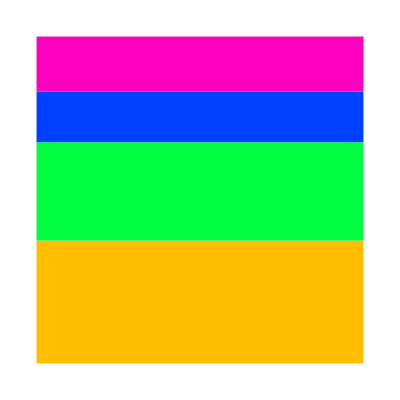

```mathematica
render2DVz@
StackerGeometry[
new2DRectangle[],
stackDs001001,
newAxisSet[newPercentageStackAxis[]]]
```

## LayoutHelper

mumble